```mathematica
Quit[]
```

```mathematica
ClearAll["`*"]
```

# #4: Final Results

## Scans and Plots

Summary Report

Written by Jae Hyeok Chang, 2022-2023

In this notebook we create the plots shown in our paper and perform the parameter space scan necessary for some of them.

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
PlotsDir=NotebookDirectory[]<>"results/plots/"
```

/home/buenabad/Documents/codes/git_codes/graphare/results/plots/

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

## Definitions

```mathematica
Clear[GeV,MeV,Mpl,mpl,second,Hz,mHz,h,ρcrit,H0,H0h1,Tγ0,gs0,ge0,gSM,Aρ,ρχi]
```

### Units

```mathematica
GeV=1;
MeV=10^-3 GeV;
TeV=10^3 GeV;
Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
second=1.519268 10^21/MeV;
Hz=1/second;
mHz=10^-3 Hz;
```

### Constants

```mathematica
h=0.67;
ρcrit=8.0992*10^-47*h^2 GeV^4;
H0=√(ρcrit/(3 mpl^2));
H0h1=H0/h;

Tγ0=(2.4*10^-4)×10^-9 GeV;
gs0=3.94;
ge0=3.38;
gSM=106.75;
```

### Useful

```mathematica
Aρ=gstar π^2/30;
ρχi=3 Hi^2 mpl^2;
```

## Packages

### InterpolatingFunctionsAnatomy

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

### PhaseTransition

```mathematica
Needs["PhaseTransition`"]
```

### DSReheating

```mathematica
Needs["DSReheating`"]
```

### dePrivFn: De-Privatize Function

Changes context from Package`Private` to Global`:

```mathematica
ContextName["PT"]="PhaseTransition`Private`";
ContextName["RH"]="DSReheating`Private`";

PrivateDict["PT"]={μ,A,λ,Δ,λbar,Mc,M,δ,T,Tc,Ts,T0};
PrivateDict["RH"]={x,rχ,rr,Hi,gstar,f,γ};
```

```mathematica
Clear[PrivFn,dePrivRule,dePrivFn]

PrivFn[ctxt_,x_]:=ToExpression[ContextName[ctxt]<>ToString[x]]
dePrivRule[ctxt_]:=dePrivRule[ctxt]=PrivFn[ctxt,#]->#&/@PrivateDict[ctxt];
dePrivFn[ctxt_,f_,x___:Null]:=(If[x===Null,If[FailureQ[PrivFn[ctxt,f]],f,PrivFn[ctxt,f]],If[FailureQ[PrivFn[ctxt,f[x]]],f[x],PrivFn[ctxt,f[x]]]])/.dePrivRule[ctxt]
```

Examples:

```mathematica
dePrivFn["PT",Ectwa,λbar]
dePrivFn["PT",EcAn,λbar]
Assuming[9/8>λbar>1,%//Simplify]
dePrivFn["PT",EcAnHot,λbar]
dePrivFn["PT",EcAn,1.1]
```

(2 π (-3+√(9-8 λbar)+4 λbar)^2)/(81 (-1+λbar)^2)

Which[0≤λbar<1,PhaseTransition`Private`EcAnCold[λbar],9/8≥λbar>1,PhaseTransition`Private`EcAnHot[λbar],λbar==1,∞]

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

10.3373

```mathematica
dePrivFn["RH",RHDict["solsAn"]["γ<<1","χD"]]
```

Get::noopen: Cannot open 1.

DSReheating`Private`RHDict[solsAn][γ $Failed,ϕD]

### FixPoligons

```mathematica
<<FixPolygons`
```

## For plots

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{purplev}{rgb}{0.5, 0, 0.5}","\\definecolor{bluearrow}{rgb}{0.12, 0.56, 1}","\\definecolor{redarrow}{rgb}{1, 0.39, 0.28}","\\definecolor{greenarrow}{rgb}{0.0941,0.545,0.133}"}];
fontsize=1.7;
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2,fticksRNoLabels,fticksR2NoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,MaTeX["10^{"<>ToString[x]<>"}",Magnification->fontsize],If[x≥0,MaTeX[ToString[10^x],Magnification->fontsize],MaTeX[ToString[10.^x],Magnification->fontsize]]]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,MaTeX["10^{"<>ToString[2x]<>"}",Magnification->fontsize],If[x≥0,MaTeX[ToString[10^x],Magnification->fontsize],MaTeX[ToString[10.^x],Magnification->fontsize]]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(* Axis for Epsilon versus mass, but with y-axis labels only every 2 decades *)
fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]),10.^(1+x+Log[10,i-10])]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],2}],1]
(* Axis for Epsilon^2 versus mass *)fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR4[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]

fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksR2NoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,"",{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]

Import["/Users/jaehyeokchang/Library/CloudStorage/Dropbox/Packages/FixPolygons-v0.2/FixPolygons.m"];
```

Import::nffil: File /Users/jaehyeokchang/Library/CloudStorage/Dropbox/Packages/FixPolygons-v0.2/FixPolygons.m not found during Import.

```mathematica
Clear[SciStr]
SciStr[x_,decimals_:0,latex_:False]:=Block[{X,pref,dex,scstr,string},

X=Log10[x];
dex=Floor[X];
pref=Round[(10^(X-dex))*10^decimals]*10^-decimals;

scstr=If[latex,StringReplace[ToString[StringForm["`1`\\times 10^(`2`)",pref,dex]],"`"->""],StringReplace[ToString[StringForm["`1`×10^(`2`)",pref,dex]],"\`"->""]];

string=If[MemberQ[{-1,0,1},dex],ToString[(Round[x*10^decimals]/10^decimals)//N],scstr];

Return[string]
]
```

## Gravitational Wave Spectra

## Stochastic Gravitational Wave Background from First Order Phase Transition (SGWB from FOPT)

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

## SGWB spectra formulas

```mathematica
Clear[fenv,Senvf,Ωenv,fsw,Sswf,Ωsw,fturb,fturb,Sturbf,Ωturb,κFn]

(*GW from envelope approximation*)
fenv[β_,vw_]:=Abs[β](0.62/(1.8-0.1vw+vw^2))*GeV/mHz(*[mHz]*);
Senvf[f_,fenv_]:=(3.8 (f/fenv)^2.8)/(1+2.8(f/fenv)^3.8);
Ωenv[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*R^2((κ α)/(1+α))^2*(Hs/β)^2((0.11 vw^3)/(0.42+vw^2))Senvf[f,Z^-1 fenv[β,vw]];

(*GW from sound waves*)
fsw[β_,vw_]:=2/(√3)×β/vw*GeV/mHz(*[mHz]*);
Sswf[f_,fsw_]:=(f/fsw)^3(7/(4+3(f/fsw)^2))^(7/2)
Ωsw[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*0.159*R^2((κ α)/(1+α))^2*(Hs/β)vw Sswf[f,Z^-1 fsw[β,vw]];

(*GW from turbulence*)
fturb[β_,vw_]:=3.5/2×β/vw*GeV/mHz(*[mHz]*);
Sturbf[f_,fturb_,hstar_]:=(f/fturb)^3/((1+f/fturb)^(11/3)(1+8π f/hstar))
Ωturb[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*20.1*R^2((κ α)/(1+α))^2*(Hs/β)vw Sturbf[f,Z^-1 fturb[β,vw],Z^-1 Hs*GeV/mHz];

(*efficiency*)
κFn[vw_,αN_]:=Block[{αn=αN,αmax,α,cs,vwJ,κA,κB,κC,κD,δκ},

αmax=1/3(1-vw)^(-13/10);
α=Min[αN,αmax];
cs=√(1/3);
vwJ=1/(1+α)(√(2/3 α+α^2)+√(1/3));
κA=vw^(6/5)(6.9α)/(1.36-0.037 √α+α);
κB=α^(2/5)/(0.017+(0.997+α)^(2/5));
κC=(√α)/(0.135+√(0.98+α));
κD=α/(0.73+0.083 √α+α);
δκ=-0.9Log[(√α)/(1+√α)];

If[0≤vw≤cs,
(cs^(11/5)κA κB)/((cs^(11/5)-vw^(11/5))κB+vw cs^(6/5)κA),
If[cs<vw<vwJ,
κB+(vw-cs)δκ+(vw-cs)^3/(vwJ-cs)^3(κC-κB-(vw-cs)δκ),
If[vwJ≤vw≤1,
((vwJ-1)^3 vwJ^(5/2)vw^(-5/2)κC κD)/(((vwJ-1)^3-(vw-1)^3)vwJ^(5/2)κC+(vw-1)^3 κD),
Print["Error"]
]
]
]
];
```

## SGWB from FOPT

```mathematica
Clear[gwSpectra]

gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γχ_,method_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwx_List:{Automatic,0,gSM,True,0},δxLargePrecAccu_List:{10^-6,10^10,30,20}]:=gwSpectra[gUVs,vwCool,coeffs,Tcrit,Hd,Γχ,method,verbose,hh,KfacΓfull,NlxExpansionSum,IRinstantVSRHwx,δxLargePrecAccu]=Block[{gdUV,gUV,gstar,Tc=Tcrit,Hi=Hd,γd=Γχ/Hd,Kfactor,full,Nlx,expansion,sum,wχ,gdIR,gd0,gIR,instantVSRH,δ,xLarge,prec,accu,xd,t0,rχ,rr,Tx,ax,tx,xDomain,xm,rCrit,xCritBoil,xpk,xCritCool,Tpk,xcs,tcs,TempEvol,gammas,vwboil=1,Tpts,tpts,λbars,Φbs,ΔVTs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,κruns,αgws,κgws,xpts,Hss,Rs,Zs,Fs,fpks,outputString, fullResult,fullResultLabels,spec,tmp},

(*distributing list arguments*)
{gdUV,gUV}=gUVs(*DS & VS UV d.o.f.*);
gstar=gdUV+gUV(*total plasma UV d.o.f.*);

{Kfactor,full}=KfacΓfull(*K-prefactor for Subscript[Γ, nucl]/𝒱; whether (Subscript[S, E]/2π)^(3/2) 0-modes prefactor included*);

{Nlx,expansion,sum}=NlxExpansionSum(* # ln(x) steps; whether Universe expansion considered; whether sum for a(x) and τ̄(x) considered*);

{gdIR,gd0,gIR,instantVSRH,wχ}=IRinstantVSRHwx(*DS d.o.f. in IR; DS-to-VS temperature ratio in IR; VS d.o.f. in IR, VS temperature in IR; whether VS reheated instantaneously; reheaton e.o.s.*);
gdIR=If[gdIR===Automatic,gdUV,gdIR];

{δ,xLarge,prec,accu}=δxLargePrecAccu(*tiny number for derivative computation, largest x-value for reheating story, precision, accuracy*);

(*the reference time, at which the χ-decays start*)
tmp=dePrivFn["RH",xd];
xd=tmp;
t0=xd/Hi;

(*the solutions to the reheating equations*)
{rχ,rr}=solEqs[γd,wχ,xLarge,prec,accu];

(*T(x)*)
Tx=TOfx[γd,gstar,Hi,wχ,xLarge,prec,accu];

(*scale factor a(x), with Subscript[a, ini]=a(x=Subscript[x, d])=1*)
ax=If[expansion==False,1,aOfx[γd,1,sum,wχ,xLarge,prec,accu]];

(*dimensionless comoving time τ̄(x)*)
tx=If[expansion==False,1,tauOfx[γd,1,1,sum,wχ,xLarge,prec,accu]];

(*its time domain*)
xDomain=(InterpolatingFunctionDomain[Tx]//Flatten);

(*deep in DS RD*)
xm=xDomain⟦-1⟧;

(*the dimensionless radiation density at critical temperature*)
rCrit=(Aρ Tc^4)/ρχi;

(*the dimensionless crossing times, at which the radiation density reaches critical temperature*)
{xCritBoil,xpk,xCritCool}=xCross[γd,rCrit,wχ,xLarge,prec,accu];

(*the peak temperature*)
Tpk=Tx[xpk];

(*a handy list for dimensionless crossing times*)
xcs={xCritBoil,xCritCool};

(*the dimensionful critical times*)
tcs=xcs/Hi;

(*reading 'method' argument to find PT temperature*)
If[MemberQ[{"analytic","semi","numeric","alt"},method]==False,Return["Please write argument 'method' a string: either 'analytic', 'semi', 'numeric', or 'alt'."]];

(*computing the PT*)
If[method=="analytic",
(*the power law behavior of the temperature as a function of time*)
gammas=gammaRate[γd,#,wχ,δ,xLarge,prec,accu]&/@xcs;
(*the parameters for the temperature evolution*)
TempEvol=Table[{gammas⟦i⟧,t0,tcs⟦i⟧},{i,2}];
,
(*the arguments for the temperature evolution*)
TempEvol={Tx,1/Hi}&/@{_,_}(*making a copy: for boiling and cooling*);
];

(*finding the properties of the phase transition: a list of pairs; the first entry being the boiling PT, the second the cooling PT*)
(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[Φ, b], Subscript[ΔV, T], Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], {Subscript[α, n]}, {Subscript[κ, run]}}*)
{Tpts,tpts,λbars,Φbs,ΔVTs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,κruns}={CheckAbort[ptParams[gstar,"hot",vwboil,TempEvol⟦1⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]],
CheckAbort[ptParams[gstar,"cold",vwCool,TempEvol⟦2⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]]}//Transpose;

(*Subscript[α, hPT]=Subscript[α, V] (V is no. 2 in {Subscript[α, n]} list), Subscript[α, cPT]=Subscript[α, ϵ] (ϵ is no. 1 in {Subscript[α, n]} list)*)
αgws={αns⟦1,2⟧,αns⟦2,1⟧};

(*Subscript[κ, hPT]=Subscript[κ, run], Subscript[κ, cPT]=Subscript[κ, sw]*)
κgws={κruns⟦1,2⟧,κFn[vwCool,αgws⟦2⟧]};

(*dimensionless times at which the PT took place*)
xpts=tpts*Hi;

(*Hubble scale at the time of GW generation, which we take to be the time of the PT: H_*=Subscript[H, PT]*)
Hss=Hi*√(rχ[#]+rr[#])&/@xpts;

(*correction due to Subscript[ρ, tot] containing a contribution from the reheaton and not only the DS radiation*)
Rs=Table[((1+αgws⟦i⟧)/(1+rχ[xpts⟦i⟧]/rr[xpts⟦i⟧])),{i,2}];

(*the extra redshift factor that GW from boiling PT undergo compared to those from cooling PT*)
Zs=redshift[γd,Hi,{#,xm},{gdUV,gUV},{gdIR,gd0,gIR},instantVSRH,wχ,xLarge,prec,accu,False]&/@xpts;

(*the prefactor for the GW SGWB Ω(f)*)
Fs=Zs^-4(Hss/(H0h1*hh))^2;

(*peak frequencies*)
fpks=Zs^-1*{fenv[βeffs⟦1⟧,1],fsw[βeffs⟦2⟧,vwCool]};

fullResult={xpk/Hi,xpk,Tpk,tcs,xcs,Tpts,tpts,tpts*Hi,λbars,Φbs,ΔVTs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,αgws,κruns,κgws,Hss,Rs,Zs,Fs,fpks};
fullResultLabels={"t_max=``","x_max=``","T_max=``","t_c=``","x_c=``","T_PT=``","t_PT=``","x_PT=``","λ̄=``","Φ_b=``","ΔV_T=``","E_c=``","S_E=``","S_E'=``","S_E''=``","Γ/V=``","β_1=``","β_2=``","n_b=``","R_b=``","⟨R⟩=``","β_eff=``","α_∞=``","{α_ϵ,α_V,α_L,α_θ}=``","α_n=``","{κ_(run, ϵ),κ_(run, V),κ_(run, L),κ_(run, θ)}=``","κ_eff=``","H_*=``","R=``","Z=``","F=``","f_pk=``"};

(*print the quantities above*)
If[verbose,
outputString=StringRiffle[Table[StringForm[fullResultLabels⟦i⟧,ScientificForm[fullResult⟦i⟧,4]],{i,Length@fullResult}],"\n"];
Print[outputString]];

spec={Ωenv[f,βeffs⟦1⟧,vwboil,Rs⟦1⟧,κgws⟦1⟧,αgws⟦1⟧,Hss⟦1⟧,Zs⟦1⟧,hh],Ωsw[f,βeffs⟦2⟧,vwCool,Rs⟦2⟧,κgws⟦2⟧,αgws⟦2⟧,Hss⟦2⟧,Zs⟦2⟧,hh]};

Return[spec]
]
```

## SGWB from FOPT experiment sensitivity

```mathematica
ΩbPISLISA[x_]:=10^-14/h^2(2.63 x^-1+3.26 10^-1 x+3.29 10^-3 x^2+4.67 10^-3 x^2.8);
ΩsPISLISA[x_]:=10^-14/h^2(3.58 10^-3 x^4+3.26 10^-1 x^-3+1.20 x^-2+2.48 x^-1+2.85 10^-1 x+1.81 10^-2 x^2+1.50 10^-3 x^3);
ΩbPISDECIGO[x_]:=10^-15/h^2(2.06 x^-1+7.61 10^-3+4.58 10^-5 x+2.19 10^-7 x^2+6.35 10^-10 x^2.8);
ΩsPISDECIGO[x_]:=10^-14/h^2(3.82 10^-1 x^-4+2.26 x^-1.5+1.10 10^-3+2.56 10^-6 x+2.91 10^-8 x^2+7.54 10^-12 x^3);
ΩbPISBBO[x_]:=10^-16/h^2(8.24 x^-1+1.61 10^-2+1.98 10^-4 x+4.24 10^-9 x^2+2.06 10^-9 x^2.8);
ΩsPISBBO[x_]:=10^-14/h^2(1.77 10^-1 x^-4+1.06 x^-1.5+1.35 10^-4+2.23 10^-6 x+1.29 10^-9 x^2+2.99 10^-12 x^3);
```

```mathematica
Clear[expsensitivity]

expsensitivity[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γχ_,method_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwx_List:{Automatic,0,gSM,True,0},δxLargePrecAccu_List:{10^-6,10^10,30,20}]:=expsensitivity[gUVs,vwCool,coeffs,Tcrit,Hd,Γχ,method,verbose,hh,KfacΓfull,NlxExpansionSum,IRinstantVSRHwx,δxLargePrecAccu]=Block[{μ,A,λ,Δ,θ,gdUV,gUV,gstar,Tc=Tcrit,Hi=Hd,γd=Γχ/Hd,Kfactor,full,Nlx,expansion,sum,wχ,gdIR,gd0,gIR,instantVSRH,δ,xLarge,prec,accu,xd,t0,rχ,rr,Tx,ax,tx,xDomain,xm,rCrit,xCritBoil,xpk,xCritCool,Tpk,xcs,tcs,TempEvol,gammas,vwboil=1,Tpts,tpts,λbars,Φbs,ΔVTs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,κruns,αgws,κgws,xpts,Hss,Rs,Zs,Fs,fpks,outputString, fullResult,fullResultLabels,tmp,fpeakboil,fpeakcool,Ωboilfpeakboil,Ωcoolfpeakcool,Ωboilfpeakcool,Ωcoolfpeakboil,spec},

{μ,A,λ}=coeffs;

(*distributing list arguments*)
{gdUV,gUV}=gUVs(*DS & VS UV d.o.f.*);
gstar=gdUV+gUV(*total plasma UV d.o.f.*);

{Kfactor,full}=KfacΓfull(*K-prefactor for Subscript[Γ, nucl]/𝒱; whether (Subscript[S, E]/2π)^(3/2) 0-modes prefactor included*);

{Nlx,expansion,sum}=NlxExpansionSum(* # ln(x) steps; whether Universe expansion considered; whether sum for a(x) and τ̄(x) considered*);

{gdIR,gd0,gIR,instantVSRH,wχ}=IRinstantVSRHwx(*DS d.o.f. in IR; DS-to-VS temperature ratio in IR; VS d.o.f. in IR, VS temperature in IR; whether VS reheated instantaneously; reheaton e.o.s.*);
gdIR=If[gdIR===Automatic,gdUV,gdIR];

{δ,xLarge,prec,accu}=δxLargePrecAccu(*tiny number for derivative computation, largest x-value for reheating story, precision, accuracy*);

(*the reference time, at which the χ-decays start*)
tmp=dePrivFn["RH",xd];
xd=tmp;
t0=xd/Hi;

(*the solutions to the reheating equations*)
{rχ,rr}=solEqs[γd,wχ,xLarge,prec,accu];

(*T(x)*)
Tx=TOfx[γd,gstar,Hi,wχ,xLarge,prec,accu];

(*scale factor a(x), with Subscript[a, ini]=a(x=Subscript[x, d])=1*)
ax=If[expansion==False,1,aOfx[γd,1,sum,wχ,xLarge,prec,accu]];

(*dimensionless comoving time τ̄(x)*)
tx=If[expansion==False,1,tauOfx[γd,1,1,sum,wχ,xLarge,prec,accu]];

(*its time domain*)
xDomain=(InterpolatingFunctionDomain[Tx]//Flatten);

(*deep in DS RD*)
xm=xDomain⟦-1⟧;

(*the dimensionless radiation density at critical temperature*)
rCrit=(Aρ Tc^4)/ρχi;

(*the dimensionless crossing times, at which the radiation density reaches critical temperature*)
{xCritBoil,xpk,xCritCool}=xCross[γd,rCrit,wχ,xLarge,prec,accu];

(*the peak temperature*)
Tpk=Tx[xpk];

(*a handy list for dimensionless crossing times*)
xcs={xCritBoil,xCritCool};

(*the dimensionful critical times*)
tcs=xcs/Hi;

(*reading 'method' argument to find PT temperature*)
If[MemberQ[{"analytic","semi","numeric","alt"},method]==False,Return["Please write argument 'method' a string: either 'analytic', 'semi', 'numeric', or 'alt'."]];

(*computing the PT*)
If[method=="analytic",
(*the power law behavior of the temperature as a function of time*)
gammas=gammaRate[γd,#,wχ,δ,xLarge,prec,accu]&/@xcs;
(*the parameters for the temperature evolution*)
TempEvol=Table[{gammas⟦i⟧,t0,tcs⟦i⟧},{i,2}];
,
(*the arguments for the temperature evolution*)
TempEvol={Tx,1/Hi}&/@{_,_}(*making a copy: for boiling and cooling*);
];

(*finding the properties of the phase transition: a list of pairs; the first entry being the boiling PT, the second the cooling PT*)
(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[Φ, b], Subscript[ΔV, T], Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], {Subscript[α, n]}, {Subscript[κ, run]}}*)
{Tpts,tpts,λbars,Φbs,ΔVTs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,κruns}={CheckAbort[ptParams[gstar,"hot",vwboil,TempEvol⟦1⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],{Tcrit,t0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.758*10^-8,0,{0,0,0,0},{0,0,0,0}}],
CheckAbort[ptParams[gstar,"cold",vwCool,TempEvol⟦2⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],{Tcrit,t0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.501*10^-11,0,{10.^-20,10.^-20,10.^-20,10.^-20},{0,0,0,0}}]}//Transpose;

(*Subscript[α, hPT]=Subscript[α, V] (V is no. 2 in {Subscript[α, n]} list), Subscript[α, cPT]=Subscript[α, ϵ] (ϵ is no. 1 in {Subscript[α, n]} list)*)
αgws={αns⟦1,2⟧,αns⟦2,1⟧};

(*Subscript[κ, hPT]=Subscript[κ, run], Subscript[κ, cPT]=Subscript[κ, sw]*)
κgws={κruns⟦1,2⟧,κFn[vwCool,αgws⟦2⟧]};

(*dimensionless times at which the PT took place*)
xpts=tpts*Hi;

(*Hubble scale at the time of GW generation, which we take to be the time of the PT: H_*=Subscript[H, PT]*)
Hss=Hi*√(rχ[#]+rr[#])&/@xpts;

(*correction due to Subscript[ρ, tot] containing a contribution from the reheaton and not only the DS radiation*)
Rs=Table[((1+αgws⟦i⟧)/(1+rχ[xpts⟦i⟧]/rr[xpts⟦i⟧])),{i,2}];

(*the extra redshift factor that GW from boiling PT undergo compared to those from cooling PT*)
Zs=redshift[γd,Hi,{#,xm},{gdUV,gUV},{gdIR,gd0,gIR},instantVSRH,wχ,xLarge,prec,accu,False]&/@xpts;

(*the prefactor for the GW SGWB Ω(f)*)
Fs=Zs^-4(Hss/(H0h1*hh))^2;

(*peak frequencies*)
fpks=Zs^-1*{fenv[βeffs⟦1⟧,1],fsw[βeffs⟦2⟧,vwCool]};
fpeakboil=fpks⟦1⟧;
fpeakcool=fpks⟦2⟧;

(*spectra at peak frequencies*)
Ωboilfpeakboil=Ωenv[fpeakboil,βeffs⟦1⟧,vwboil,Rs⟦1⟧,κgws⟦1⟧,αgws⟦1⟧,Hss⟦1⟧,Zs⟦1⟧,hh];Ωboilfpeakcool=Ωenv[fpeakcool,βeffs⟦1⟧,vwboil,Rs⟦1⟧,κgws⟦1⟧,αgws⟦1⟧,Hss⟦1⟧,Zs⟦1⟧,hh];
Ωcoolfpeakcool=Ωsw[fpeakcool,βeffs⟦2⟧,vwCool,Rs⟦2⟧,κgws⟦2⟧,αgws⟦2⟧,Hss⟦2⟧,Zs⟦2⟧,hh];
Ωcoolfpeakboil=Ωsw[fpeakboil,βeffs⟦2⟧,vwCool,Rs⟦2⟧,κgws⟦2⟧,αgws⟦2⟧,Hss⟦2⟧,Zs⟦2⟧,hh];

(* parameters *)
Δ=(4 A^2)/(3 λ μ^2);
θ=Tpk/Tcrit;

spec={1/θ,Δ,{fpeakboil,fpeakcool},{Ωboilfpeakboil,Ωcoolfpeakcool},{Ωboilfpeakcool,Ωcoolfpeakboil},{ΩbPISBBO[fpeakboil],ΩsPISBBO[fpeakcool]},{ΩbPISLISA[fpeakboil],ΩsPISLISA[fpeakcool]},Tpts,tpts,λbars,Φbs,ΔVTs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αgws,κgws,Rs,Zs,{μ,A,λ,Tcrit,γd,vwCool,gstar,Hi}};
Return[spec]
]
```

## Runs

### Test run

{μ,A,λ}={1,0.798436,1}

T_c exists: True

f=2.40274

-Graphics-

{x_c1,x_max,x_c2}={0.003,0.148,2.413}

T_max=1000. GeV

λ̄(T_max)=1.13235 (should be smaller than 9/8=1.125)

S_E(T_max)=(5.80998+0.945598 ⅈ) Null

log_10(Γ/𝒱)_T_max=(27.631-(5.80998+0.945598 ⅈ) Null)/Log[10]

S_E(T_max)/(4×ln[m_Pl/T_c])=(0.0402108+0.00654447 ⅈ) Null

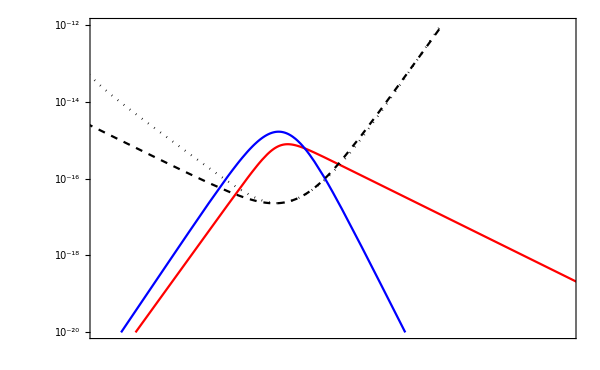

{(5.00683×10^-22 f^2.8)/(1+1.80437×10^-9 f^3.8),1.86156×10^-19 f^3 (1/(4+0.0000747446 f^2))^(7/2)}

```mathematica
verbose=True;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.1;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

(*
(*VERY STRONG FOPT: Subscript[α, n]>1 ⇒ vacuum energy is important ⇒ evolution during RH is suspect*)
μ=10;
λ=3;*)

{θinv,Δ}={0.5,0.85};

μ=1;
λ=1;
(*Δ=8/9+0.02;*)
(*Δ=8/9-0.0001;*)
(*Δ=0.5;*)
A=(A/.(dePrivFn["PT",ARule]));
pars={μ,A,λ};
Print["{μ,A,λ}=",pars]
Print["T_c exists: ",dePrivFn["PT",cond1,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧]]

Tcr=10^3 GeV/2;

gam=10;
Tmax[eff_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];
efffind[θinv_]:=effv/.FindRoot[Tcr/Tmax[effv]==θinv,{effv,1}]//Quiet;
eff=efffind[θinv];
Print["f=",eff]

{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;

Hdec=Hi;
Gam=gam*Hdec;

tofx=TOfx[Gam/Hdec,gs,Hdec];
dlntdt[x_]=Hdec*D[tofx[x],x]/tofx[x];
d2lntdt2[x_]=Hdec*D[dlntdt[x],x];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];


legendfont2=1.6;
LogLogPlot[{rχ[dx],rr[dx],rCrit},{dx,10^-5,(*domain⟦-1⟧-2/3*)10^2},Frame->True,ImageSize->600,PlotRange->{{10^-4,10^2},{10^-4,3}},PlotStyle->{Blue,Red,{Black,Dashed}},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\rho/\\rho_{\\phi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_\\phi/\\rho_{\\phi,i}",Magnification->legendfont2],MaTeX["\\rho_r/\\rho_{\\phi,i}",Magnification->legendfont2]},Spacings->.1],{0.87,0.8}],GridLines->{{xC1,xMAX,xC2},None},Epilog->{Inset[MaTeX["\\gamma = 10",Magnification->1.3],Scaled[{0.1,0.07}]],Inset[MaTeX["\\rho_c = 0.03 \\rho_{\\phi,i}",Magnification->1.3],Scaled[{0.12,0.59}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.232,0.3}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.713,0.3}]],Inset[Rotate[MaTeX["t=t_\\textrm{max}",Magnification->1.4],90°],Scaled[{0.51,0.3}]]}]

Print["{x_c1,x_max,x_c2}=",Round[#,0.001]&/@{xC1,xMAX,xC2}]
Print["T_max=",Tmx," GeV"]
Print["λ̄(T_max)=",(dePrivFn["PT",λbar]/.dePrivFn["PT",McλbarToCoeffs])/.{Tc->Tcr,T->Tmx}," (should be smaller than 9/8=1.125)"]
Print["S_E(T_max)=",SETemp[pars,Tcr,Tmx]]
Print["log_10(Γ/𝒱)_T_max=",Γnucl[pars,Tcr,Tmx,1,False,True]]
Print["S_E(T_max)/(4×ln[m_Pl/T_c])=",SETemp[pars,Tcr,Tmx]/(4Log[mpl/Tcr])]

(*reheating IR quantities*)
IRs={Automatic,0,gSM,True,0};


gwS=gwSpectra[UVs,vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}];

LogLogPlot[Evaluate[Flatten[{gwS,{ΩbPISBBO[f],ΩsPISBBO[f]}},1]],{f,0.001,10^9},PlotStyle->{Red,Blue,{Black,Dashed},{Black,Dotted}},Frame->True,PlotRange->{{1,10^6},{10^-20,10^-12}},ImageSize->600,Frame->True,FrameTicks->{{fticksR2[10^-80,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\text{hGW}",Magnification->1.2],MaTeX["\\Omega_\\text{cGW}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{bc}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}],Epilog->{Inset[MaTeX["T_c = 500~\\textrm{GeV},~\\gamma = 10,~\\lambda=1,~\\mu=1, g_* = 10,~v_w^c=10^{-2}",Magnification->1.1],Scaled[{0.35,0.93}]]}]

gwS

(*Clear[gDSUV,gVSUV,gs,vwc,μ,A,λ,Δ,pars,Tcr,eff,gam,regime,Hdec,Gam,verbose,UVs,IRs,gwS,p1,p2,tofx,dlntdt,d2lntdt2,xC1,xMAX,xC2,Tmx,domain,Tpt,tpt,n0,Lmlnh1,Lmlnh2,Lmlnh3,LnbLx,xData,yData]*)
```

```mathematica
expsensitivity[UVs,vwc,{μ,A,λ},Tcr,Hi,Gam,"numeric",verbose,h,{1,False},{250,False,True},IRs,{10^-6,10^10,30,20}]
```

{0.5,0.85,{251.566,194.686},{9.0934×10^-16,1.92839×10^-15},{8.19496×10^-16,1.72033×10^-15},{2.44575×10^-17,2.29522×10^-17},{5.54733×10^-10,1.14833×10^-7},{742.149,314.75},{2.70132×10^10,1.09738×10^13},{1.09637,0.731141},{2061.26,1200.01},{1.12748×10^11,1.40246×10^10},{77770.,36675.7},{104.79,116.523},{-6.67966×10^-9,-2.73625×10^-11},{6.83292×10^-19,9.40422×10^-24},{9.37824×10^-35,2.4348×10^-41},{6.71154×10^-9,2.71921×10^-11},{-6.84658×10^-19,-9.38967×10^-24},{8.76883×10^-27,5.647×10^-31},{4.84938×10^8,1.20984×10^10},{2.20508×10^10,7.08627×10^11},{6.04033×10^-9,2.42114×10^-11},{1.17239,2.20918},{0.112971,0.0653302},{10.3591,0.0202979},{0.170559,1.06533},{8.37666×10^15,2.18167×10^15},{1,0.798436,1,500,10.,0.1,10,6.2061×10^-13}}

### General Plots

```mathematica
Tcr=500;

μ=1;
λ=1;
Δ=.85;

V[Φ_,T_]:=μ^2/2(T^2-T0^2)Φ^2-A/3 T Φ^3+λ/(4!)Φ^4;

A=1/2 √3 √Δ √λ μ;
T0=(Tcr Sqrt[-((4 A^2)/(3 λ))+μ^2])/μ;
Ts=Tcr/Sqrt[1+A^2/(8 A^2-6 λ μ^2)];

Tba=0.8Tcr;
Φba=x/.Solve[D[V[x,Tba],x]==0,x][[2]];
Vba=V[Φba,Tba]/Tcr^4;

Φc=x/.Solve[D[V[x,Tcr],x]==0,x][[2]];

Tca=1.2Tcr;
Φca=x/.Solve[D[V[x,Tca],x]==0,x][[2]];
Vca=V[Φca,Tca]/Tcr^4;

rpoint=0.03;

redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];

Show[Plot[Evaluate[{V[Φ,Tba],V[Φ,Tcr],V[Φ,Tca]}/Tcr^4],{Φ,-Tcr,5Tcr},PlotRange->{{-.8Tcr,5.5Tcr},{-.3,1}},Frame->False,ImageSize->600,PlotStyle->{Blue,Black,Red},Ticks->{None,None},Background->White,GridLines->{None,{0}},Epilog->{Inset[Rotate[MaTeX["V(\\Phi)",Magnification->1.7],90°],Scaled[{0.105,0.9}]],Inset[MaTeX["\\Phi",Magnification->1.7],Scaled[{0.96,0.26}]],Inset[MaTeX["\\color{blue}{T_0<T<T_c}",Magnification->1.5],Scaled[{0.73,0.15}]],Inset[MaTeX["T=T_c",Magnification->1.5],Scaled[{0.8,0.45}]],Inset[MaTeX["\\color{red}{T_c<T<T_1}",Magnification->1.5],Scaled[{0.91,0.87}]],Inset[Rotate[MaTeX["\\textrm{hPT}",Magnification->1.5],20°],Scaled[{0.5,0.5}]],Inset[Rotate[MaTeX["\\textrm{cPT}",Magnification->1.5],-12°],Scaled[{0.33,0.155}]]}],Graphics[{Black,PointSize[rpoint],Point[{0,rpoint}]}],Graphics[{Black,PointSize[rpoint],Point[{Φba,Vba+rpoint}]}](*,Graphics[{Black,PointSize[rpoint],Point[{Φc,rpoint}]}]*),Graphics[{Black,PointSize[rpoint],Point[{Φca,Vca+rpoint}]}],Graphics[{bluearrowcolor,Thickness[0.005],{Arrowheads[Large],Arrow[{0.05{Φba,Vba}+{0,rpoint},0.95{Φba,Vba}+{0,rpoint}}]}}],Graphics[{redarrowcolor,Thickness[0.005],{Arrowheads[Large],Arrow[{0.95{Φca,Vca}+{0,rpoint},0.05{Φca,Vca}+{0,rpoint}}]}}]]
```

-Graphics-

```mathematica
gamtab={0.01,0.1,1,10,100};
rtab=Flatten[Table[solEqs[gamtab[[i]]],{i,1,Length[gamtab]}],1];
color=ColorData[{"Rainbow",{1,Length[gamtab]}}];
plotstylespec=Flatten[Table[{{Line,color[i]},{Dashed,color[i]}},{i,1,Length[gamtab]}],1];
legendfont=1.2;
Show[LogLogPlot[Evaluate[Table[rtab[[i]][dx],{i,1,Length[rtab]}]],{dx,10^-4,10^4},Frame->True,ImageSize->600,PlotRange->{{10^-4,10^3},{10^-6,10}},PlotStyle->plotstylespec,FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["x=H_i t",Magnification->2],MaTeX["r = \\rho/\\rho_{\\chi,i}",Magnification->2]}],Graphics[Inset[Framed[Column[Flatten[{{Row[{LineLegend[{Black},{MaTeX["r_\\chi",Magnification->legendfont]},LegendMarkerSize->{30,10}]}],Row[{LineLegend[{Dashed},{MaTeX["r_r",Magnification->legendfont]},LegendMarkerSize->{30,10}]}]},Table[Row[{LineLegend[{color[i]},{MaTeX["\\gamma = "<>ToString[gamtab[[i]]],Magnification->legendfont]}]}],{i,1,Length[gamtab]}]},1],Spacings->-.5],Background->None,FrameStyle->None,RoundingRadius->5],Scaled[{.9,.68}]]]]
```

-Graphics-

```mathematica
Clear[bubTab,bubFn,rmaxTab]
bubbleDir=NotebookDirectory[]<>"results/phase_transition/bubbles/";
fnsLambdaDir=NotebookDirectory[]<>"results/phase_transition/fns_lambda/";
λbarList=Table[lb,{lb,0.01,0.99,0.005}];
λbarList=λbarList~Join~Table[lb,{lb,1.01,1.124,0.001}];

λbarString[λbar_]:=Module[{decimals,lbStr},
decimals=IntegerString[Round[1000*(λbar-IntegerPart[λbar])],10,3];
lbStr=ToString[IntegerPart[λbar]]<>"."<>decimals;
lbStr
];

For[i=1,i≤(λbarList//Length),i++,
λbar=λbarList⟦i⟧;
fileName="bubble_lb-"<>λbarString[λbar]<>".csv";
bubTab[i]=Import[bubbleDir<>fileName];
bubFn[i]=Interpolation[bubTab[i],InterpolationOrder->2]
]

rmaxTab=Import[fnsLambdaDir<>"rmax.csv"];

Clear[i,λbar,fileName]
```

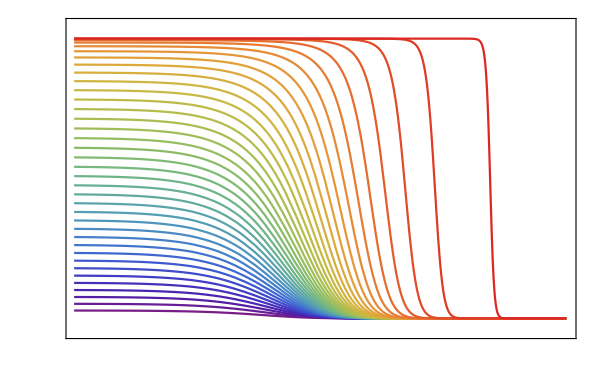

```mathematica
labelfont=1.7;
λbarcList=Table[lb,{lb,0.01,.99,0.005}];
step=5;
color=ColorData[{"Rainbow",{1,Length[λbarcList]/step}}];
plotstylespec=Table[{Line,color[i]},{i,1,Length[λbarcList]/step}];
LogLinearPlot[Evaluate[Table[bubFn[step i][r],{i,1,Length[λbarcList]/step}]],{r,0,100},PlotRange->{{0.1,10^2},{-0.05,1.05}},PlotStyle->plotstylespec,Frame->True,ImageSize->600,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,-0.1,1.1,.1}],Table[{i,""},{i,-0.1,1.1,.1}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},FrameLabel->{MaTeX["\\bar{r}",Magnification->2],MaTeX["\\bar\\Phi_\\textrm{bub}",Magnification->2]},Background->White,PlotLegends->Placed[BarLegend[{"Rainbow",(*{λbarcList[[1]],λbarcList[[-1]]}*){0,1}},LegendLabel->MaTeX["\\bar\\lambda",Magnification->1.4],LegendMarkerSize->250,LabelStyle->{FontSize->15}],{0.94,.5}]]
```

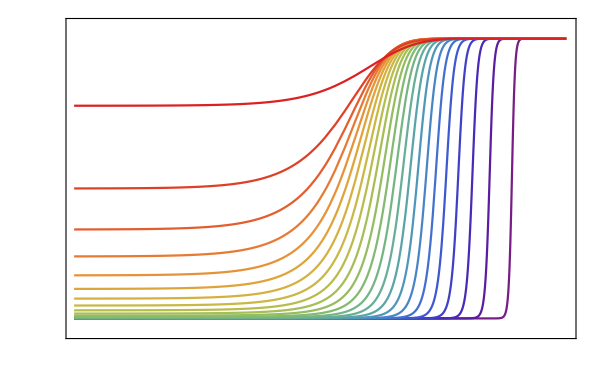

```mathematica
λbarhList=Table[lb,{lb,1.01,1.124,0.001}];
step=5;
color=ColorData[{"Rainbow",{1,Length[λbarhList]/step}}];
plotstylespec=Table[{Line,color[i]},{i,1,Length[λbarhList]/step}];
LogLinearPlot[Evaluate[Table[bubFn[Length[λbarcList]+step i][r],{i,1,Length[λbarhList]/step}]],{r,0,100},PlotRange->{{10^-1,10^2},{-0.05,1.05}},PlotStyle->plotstylespec,Frame->True,ImageSize->600,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,-0.1,1.1,.1}],Table[{i,""},{i,-0.1,1.1,.1}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},FrameLabel->{MaTeX["\\bar{r}",Magnification->2],MaTeX["\\bar\\Phi_\\textrm{bub}",Magnification->2]},Background->White,PlotLegends->Placed[BarLegend[{"Rainbow",{λbarhList[[1]],λbarhList[[-1]]}(*{1,9/8}*)},LegendLabel->MaTeX["\\bar\\lambda",Magnification->1.4],LegendMarkerSize->250,LabelStyle->{FontSize->15}],{0.945,.45}]]
```

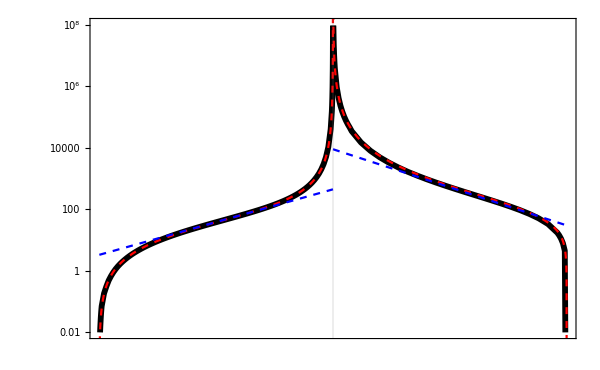

```mathematica
λbarcList=DeleteDuplicates[Table[lb,{lb,0,.01,0.001}]~Join~Table[lb,{lb,0.01,0.99,0.01}]~Join~Table[lb,{lb,0.99,1.01,0.0002}]~Join~Table[lb,{lb,1.01,1.12,0.005}]~Join~Table[lb,{lb,1.12,1.125,0.001}]];
μ=1;
λ=1;
Δ=.8;
A=1/2 √3 √Δ √λ μ;
coeffs={μ,A,λ};
Tcr=500;
Tλbar[λbar_]:=Tcr Sqrt[(1-Δ)/(1-Δ*λbar)];
SEtable=Table[{λbar,((μ √Δ)/λ)^-1 SETemp[coeffs,Tcr,Tλbar[λbar]]},{λbar,λbarcList}];

labelfont=1.7;
Show[ListPlot[SEtable,Joined->True,ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotStyle->{{Black,Thickness[0.007]}},GridLines->{{1},None},Frame->True,PlotRange->{{0,9/8},{10^-2,10^8}},ImageSize->600,Frame->True,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.2}]~Join~{{1.025,""},{1.05,MaTeX[1.05,Magnification->labelfont]},{1.075,""},{1.1,MaTeX[1.1,Magnification->labelfont]},{9/8,MaTeX["9/8",Magnification->labelfont]}},Table[{i,""},{i,0,1,.2}]~Join~Table[{i,""},{i,1.025,1.125,0.025}]}},Background->White,FrameLabel->{MaTeX["\\bar\\lambda",Magnification->2],Rotate[MaTeX["\\frac{\\lambda S}{\\mu \\sqrt{\\Delta}}",Magnification->1.6],-90°]}(*,PlotLegends->Placed[LineLegend[{MaTeX["\\bar\\lambda",Magnification->1.2],MaTeX["\\frac{\\lambda S_E}{\\mu \\sqrt{\\Delta}}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{env}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}]*)],(*LogPlot[{(3/2(9+3 √(9-8λbar)-4λbar)/(√λbar))(8π)/(81(λbar-1)^2)},{λbar,0.3,1.15},PlotRange->All,PlotStyle->{{Dashed,Darker@Green}}],LogPlot[{(3/2(9+3 √(9-8λbar)-4λbar)/(√λbar))2.16 λbar^2},{λbar,0,.5},PlotRange->All,PlotStyle->{{Dashed,Brown}}],LogPlot[{(3/2(9+3 √(9-8λbar)-4λbar)/(√λbar))113(9/8-λbar)^(3/4)},{λbar,1.05,9/8},PlotRange->All,PlotStyle->{{Dashed,Purple}}],*)(*Plot[{1.7((9+3 √(9-8λbar)-4λbar)/(1-λbar)^2)λbar^(3/2)},{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotRange->All,PlotStyle->{{Dashed,Red}}],Plot[{2.5((9+3 √(9-8λbar)-4λbar)/(1-λbar)^2)(9/8-λbar)^(3/4)/λbar^(1/2)},{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotRange->All,PlotStyle->{{Dashed,Red}}]*)
Plot[{24((3+√(9-8λbar))/4)^2((1.13-λbar)^0.91 λbar^(3/2))/(1-λbar)^2},{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotRange->All,PlotStyle->{{Dashed,Red}}],
Plot[{20((3+√(9-8λbar))/4)(9/8-λbar)^(3/4)/(λbar^(1/2)(1-λbar)^2)},{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotRange->All,PlotStyle->{{Dashed,Red}}],
Plot[{Exp[1.2+4.9λbar]},{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotRange->All,PlotStyle->{{Dashed,Blue}}],
Plot[{Exp[54.7-45.6λbar]},{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotRange->All,PlotStyle->{{Dashed,Blue}}]]
```

```mathematica
Clear[λ,μ,Δ,λbar]
NSolve[(1+λ/(12 μ^2 Δ)(4/(3+√(9-8λbar)))^2)^(3/2)-1==1/2,Δ]
NSolve[(1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2)==0,Δ]
```

{{Δ→(4.29594 λ)/((3.+√(9.-8. λbar))^2 μ^2)}}

{{Δ→(0.25 (9.+3. √(9.-8. λbar)-1. √((-9.-3. √(9.-8. λbar))^2-16. λbar^2)))/λbar^2},{Δ→(0.25 (9.+3. √(9.-8. λbar)+√((-9.-3. √(9.-8. λbar))^2-16. λbar^2)))/λbar^2}}

```mathematica
labelfont=1.7;
legendfont=1.3;

Tcr=10^3 GeV;
TofΔλbar[Δ_,λbar_]:=Tcr √((1-Δ)/(1-Δ λbar));

Δdaisyfunc[λbar_,μ_,λ_]:=(4.2959381983300755 λ)/((3.+√(9.-8. λbar))^2 μ^2);
Δrunawayfunc[λbar_]:=(0.25 (9.+3. √(9.-8. λbar)-1. √((-9.-3. √(9.-8. λbar))^2-16. λbar^2)))/λbar^2;

Show[Plot[{Δdaisyfunc[λbar,1,2]},{λbar,0,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},None},PlotRange->{{0,9/8},{0,1}},Frame->True,AspectRatio->1,ImageSize->600,Background->White,Filling->Bottom,PlotStyle->None,FillingStyle->{1->{Lighter[Gray,.3]}},FrameLabel->{MaTeX["\\bar{\\lambda}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,2,.1}],Table[{i,""},{i,0,1,.1}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.2}]~Join~{{1.025,""},{1.05,MaTeX[1.05,Magnification->labelfont]},{1.075,""},{1.1,MaTeX[1.1,Magnification->labelfont]},{9/8,MaTeX["9/8",Magnification->labelfont]}},Table[{i,""},{i,0,1,.2}]~Join~Table[{i,""},{i,1.025,1.125,0.025}]}},Epilog->{Inset[MaTeX["\\kappa_\\Phi = 10^2",Magnification->1.3],Scaled[{0.8,0.81}]],Inset[MaTeX["\\kappa_\\Phi = 10",Magnification->1.3],Scaled[{0.8,0.58}]],Inset[MaTeX["\\kappa_\\Phi = 1",Magnification->1.3],Scaled[{0.8,0.315}]],Inset[MaTeX["\\kappa_\\Phi = 10^{-1}",Magnification->1.3],Scaled[{0.8,0.225}]],Inset[MaTeX["\\kappa_\\Phi = 10^{-2}",Magnification->1.3],Scaled[{0.8,0.17}]]}],Plot[{Δdaisyfunc[λbar,1,1]},{λbar,0,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},None},PlotRange->{{0,9/8},{0,1}},Frame->True,AspectRatio->1,ImageSize->600,Background->White,Filling->Bottom,PlotStyle->None,FillingStyle->{1->{Lighter[Gray,.5]}}],Plot[{Δdaisyfunc[λbar,1,1/2]},{λbar,0,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},None},PlotRange->{{0,9/8},{0,1}},Frame->True,AspectRatio->1,ImageSize->600,Background->White,Filling->Bottom,PlotStyle->None,FillingStyle->{1->{Lighter[Gray,.7]}}],
Plot[{Δrunawayfunc[λbar]},{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},None},PlotRange->{{0,9/8},{0,1}},Frame->True,AspectRatio->1,ImageSize->600,Background->White,Filling->Bottom,PlotStyle->None,FillingStyle->{1->{Darker@Green,Opacity[.2]}}],
Plot[{Δrunawayfunc[λbar]},{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},None},PlotRange->{{0,9/8},{0,1}},Frame->True,AspectRatio->1,ImageSize->600,Background->White,Filling->Top,PlotStyle->None,FillingStyle->{1->{Darker@Green,Opacity[.2]}}],Block[{μ=1,λ=1,gs=10},ContourPlot[dePrivFn["PT",κrun,gs,{μ,1/2 √3 √Δ √λ μ,λ},Tcr,TofΔλbar[Δ,λbar]],{λbar,1,9/8},{Δ,0,1},Contours->Table[10^i,{i,-2,3}],ContourShading->None,ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},None},PlotRange->{{0,9/8},{0,1}},ContourStyle->{{Dotted,Thickness[0.003]}}]],
Graphics[Inset[Framed[Column[{Row[{SwatchLegend[{Lighter[Gray,.3]},{MaTeX["\\textrm{Daisy excluded},~\\frac{\\lambda}{\\mu^2}=2",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Daisy excluded},~\\frac{\\lambda}{\\mu^2}=1",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.7]},{MaTeX["\\textrm{Daisy excluded},~\\frac{\\lambda}{\\mu^2}=\\frac{1}{2}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Darker@Green,.7]},{MaTeX["\\textrm{Runaway}",Magnification->legendfont]}]}]},Spacings->-.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.24,.75}]]]]
```

-Graphics-

```mathematica
Tcr=10^3 GeV;
legendfont=1.2;
labelfont=1.7;
TofΔλbar[Δ_,λbar_]:=Tcr √((1-Δ)/(1-Δ λbar));
μ=1;
λ=1;
Δ=.5;
nuclappplot[μ_,λ_,Δ_,lighter_]:=
Show[Plot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,TofΔλbar[Δ,λbar],1,True,False]/(TofΔλbar[Δ,λbar])^4],{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},GridLines->{{1},None},PlotStyle->{Lighter[Blue,lighter]},PlotRange->{{0,9/8},{10^-70,10^2}},Frame->True,ImageSize->600,Background->White,FrameLabel->{MaTeX["\\bar\\lambda",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/T^4)",Magnification->1.7]},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-100,100,10}],Table[{10^i,""},{i,-100,100,10}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.2}]~Join~{{1.025,""},{1.05,MaTeX[1.05,Magnification->labelfont]},{1.075,""},{1.1,MaTeX[1.1,Magnification->labelfont]},{9/8,MaTeX["9/8",Magnification->labelfont]}},Table[{i,""},{i,0,1,.2}]~Join~Table[{i,""},{i,1.025,1.125,0.025}]}}],Plot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,TofΔλbar[Δ,λbar],1,True,False]/(TofΔλbar[Δ,λbar])^4],{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotStyle->{Lighter[Red,lighter]}]]//Quiet;

Show[nuclappplot[1,√(.5),.5,0],nuclappplot[.7,√(.5),.5,.5],nuclappplot[.4,√(.5),.5,.7],nuclappplot[.1,√(.5),.5,.9],Plot[10^-60,{λbar,0,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotStyle->{{Black,Dashed}}],Graphics[Inset[Framed[Column[{Row[{LineLegend[{Lighter[Blue,0]},{MaTeX["\\textrm{cPT}",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Red,0]},{MaTeX["\\textrm{hPT}",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,0]},{MaTeX["\\frac{\\mu\\sqrt{\\Delta}}{\\lambda}=1",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,.5]},{MaTeX["\\frac{\\mu\\sqrt{\\Delta}}{\\lambda}=0.7",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,.7]},{MaTeX["\\frac{\\mu\\sqrt{\\Delta}}{\\lambda}=0.4",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,.9]},{MaTeX["\\frac{\\mu\\sqrt{\\Delta}}{\\lambda}=0.1",Magnification->legendfont]}]}](*,Row[{LineLegend[{Dashed},{MaTeX["\\Gamma/\\mathcal{V}\\sim H^4",Magnification->legendfont]},LegendMarkerSize->{23,10}]}],Row[{LineLegend[{White},{MaTeX["(T_c=1~\\textrm{TeV})",Magnification->legendfont]},LegendMarkerSize->{15,10}]}]*)},Spacings->-1.3],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.145,.36}]]]]
```

-Graphics-

```mathematica
Tcr=10^3 GeV;
legendfont=1.2;
labelfont=1.7;
TofΔλbar[Δ_,λbar_]:=Tcr √((1-Δ)/(1-Δ λbar));
μ=1;
λ=1;

dlnSdlnTplot[Δv_,lighter_]:=Block[{Δ=Δv,A=1/2 √3 √Δv √λ μ},
Show[Plot[dePrivFn["PT",dSdlnT,{μ,A,λ},Tcr,TofΔλbar[Δ,λbar]]/SETemp[{μ,A,λ},Tcr,TofΔλbar[Δ,λbar]],{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},GridLines->{{1},None},PlotStyle->{Lighter[Blue,lighter]},PlotRange->{{0,9/8},{10^0,10^4}},Frame->True,ImageSize->600,Background->White,FrameLabel->{MaTeX["\\bar\\lambda",Magnification->2],MaTeX["\\vert d \\ln S/ d \\ln T \\vert",Magnification->1.7]},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.2}]~Join~{{1.025,""},{1.05,MaTeX[1.05,Magnification->labelfont]},{1.075,""},{1.1,MaTeX[1.1,Magnification->labelfont]},{9/8,MaTeX["9/8",Magnification->labelfont]}},Table[{i,""},{i,0,1,.2}]~Join~Table[{i,""},{i,1.025,1.125,0.025}]}}],Plot[-dePrivFn["PT",dSdlnT,{μ,A,λ},Tcr,TofΔλbar[Δ,λbar]]/SETemp[{μ,A,λ},Tcr,TofΔλbar[Δ,λbar]],{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotStyle->Lighter[Red,lighter],PlotRange->All],Plot[{9.8/Δ(1-Δ λbar)},{λbar,0,1},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotStyle->{Lighter[Blue,lighter],Dashed}],Plot[{91/Δ(1-Δ λbar)},{λbar,1,9/8},ScalingFunctions->{{If[#<1,#,8#-7]&,If[#<1,#,(#+7)/8]&},"Log"},PlotStyle->{Lighter[Red,lighter],Dashed}]]
];
Show[dlnSdlnTplot[0.2,0.8],dlnSdlnTplot[0.5,.5],dlnSdlnTplot[0.8,0],Graphics[Inset[Framed[Column[{Row[{LineLegend[{Lighter[Blue,0]},{MaTeX["\\textrm{cPT}",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Red,0]},{MaTeX["\\textrm{hPT}",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,0.8]},{MaTeX["\\Delta=0.2",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,0.5]},{MaTeX["\\Delta=0.5",Magnification->legendfont]}]}],Row[{LineLegend[{Lighter[Black,0]},{MaTeX["\\Delta=0.8",Magnification->legendfont]}]}]},Spacings->-1.3],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.25,.75}]]]]
```

-Graphics-

```mathematica
polygon2FilledCurve=#/. g_GraphicsComplex:>(g/. {Polygon[pts:{{__Integer}..}]:>FilledCurve/@Thread[Line[pts]],Polygon[pts:{__Integer}]:>FilledCurve[Line[pts]]})/.
{Polygon[pts:{_?(MatrixQ[#,NumericQ]&)..}]:>FilledCurve/@Thread[Line[pts]],Polygon[pts_/;MatrixQ[pts,NumericQ]]:>FilledCurve[Line[pts]]}&
```

#1/.g_GraphicsComplex:>(g/.{Polygon[pts:{{__Integer}..}]:>FilledCurve/@Thread[Line[pts]],Polygon[pts:{__Integer}]:>FilledCurve[Line[pts]]})/.{Polygon[pts:{_?(MatrixQ[#1,NumericQ]&)..}]:>FilledCurve/@Thread[Line[pts]],Polygon[pts_/;MatrixQ[pts,NumericQ]]:>FilledCurve[Line[pts]]}&

```mathematica
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
greenarrowcolor=Lighter@RGBColor[24/255,139/255,34/255];

arrowhead=.1;
arrowthickness=0.02;

bubblecptplot=Show[RegionPlot[x^2+y^2<1,{x,.9,1.1},{y,-.1,.1},BoundaryStyle->None,PlotStyle->{Lighter[bluearrowcolor,.9]},Frame->True,FrameTicks->None,PlotRangePadding->0,Background->White,ImageSize->400,AspectRatio->1,Epilog->{Inset[MaTeX["\\begin{aligned}\\left<\\Phi\\right> &= 0 \\\\ m &=0 \\end{aligned}",Magnification->1.7],Scaled[{0.75,0.9}]],Inset[MaTeX["\\begin{aligned}\\left<\\Phi\\right> &\\neq 0 \\\\ m &>0 \\end{aligned}",Magnification->1.7],Scaled[{0.25,0.9}]],Inset[MaTeX["\\color{greenarrow}\\textrm{Flux}~(\vec{v}=-v_w)",Magnification->2],Scaled[{0.78,0.56}]],Inset[MaTeX["\\color{bluearrow}\\textrm{Friction}",Magnification->2],Scaled[{0.35,0.41}]],Inset[MaTeX["\\textrm{cPT}",Magnification->1.8],Scaled[{0.92,0.05}]]}],ContourPlot[x^2+y^2==1,{x,.9,1.1},{y,-.1,.1},ImageSize->400,ContourStyle->{Directive[Thickness[0.05],Lighter[bluearrowcolor,.7]]},Frame->True,FrameTicks->None,PlotRangePadding->0,Background->White,AspectRatio->1],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.9,.5}],Scaled[{.6,.5}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.9,.8}],Scaled[{.6,.8}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.9,.2}],Scaled[{.6,.2}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.35,.5}],Scaled[{.15,.5}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.35,.8}],Scaled[{.15,.8}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.35,.2}],Scaled[{.15,.2}]}]}}],Graphics[{Lighter[bluearrowcolor,.7],Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.45,.35}],Scaled[{.25,.35}]}]}}],Graphics[{Lighter[bluearrowcolor,.7],Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.45,.65}],Scaled[{.25,.65}]}]}}]]
```

Syntax::stresc: Unknown string escape \v.

-Graphics-

```mathematica
Export["../plots/bubblecpt.pdf",bubblecptplot];
```

```mathematica
Show[RegionPlot[x^2+y^2<1,{x,.9,1.1},{y,-.1,.1},BoundaryStyle->None,PlotStyle->{Lighter[redarrowcolor,.9]},Frame->True,FrameTicks->None,PlotRangePadding->0,Background->White,ImageSize->400,AspectRatio->1,Epilog->{Inset[MaTeX["\\begin{aligned}\\left<\\Phi\\right> &\\neq 0 \\\\ m &>0 \\end{aligned}",Magnification->1.7],Scaled[{0.75,0.9}]],Inset[MaTeX["\\begin{aligned}\\left<\\Phi\\right> &= 0 \\\\ m &=0 \\end{aligned}",Magnification->1.7],Scaled[{0.25,0.9}]],Inset[MaTeX["\\color{greenarrow}\\textrm{Flux}~(\vec{v}=-v_w)",Magnification->2],Scaled[{0.78,0.56}]],Inset[MaTeX["\\color{redarrow}\\textrm{Anti-friction}",Magnification->2],Scaled[{0.7,0.41}]],Inset[MaTeX["\\textrm{hPT}",Magnification->1.8],Scaled[{0.92,0.05}]]}],ContourPlot[x^2+y^2==1,{x,.9,1.1},{y,-.1,.1},ImageSize->400,ContourStyle->{Directive[Thickness[0.05],Lighter[redarrowcolor,.7]]},Frame->True,FrameTicks->None,PlotRangePadding->0,Background->White,AspectRatio->1],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.9,.5}],Scaled[{.6,.5}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.9,.8}],Scaled[{.6,.8}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.9,.2}],Scaled[{.6,.2}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.45,.5}],Scaled[{.05,.5}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.45,.8}],Scaled[{.05,.8}]}]}}],Graphics[{greenarrowcolor,Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.45,.2}],Scaled[{.05,.2}]}]}}],Graphics[{Lighter[redarrowcolor,.7],Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.55,.35}],Scaled[{.75,.35}]}]}}],Graphics[{Lighter[redarrowcolor,.7],Thickness[arrowthickness],{Arrowheads[arrowhead],Arrow[{Scaled[{.55,.65}],Scaled[{.75,.65}]}]}}]]
```

-Graphics-

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , γ=0.1

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;
gam=0.1;

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr)]];

efffind[θinv_]:=effv/.FindRoot[Tcr/Tmax[effv]==θinv,{effv,effmin,effmin,effmax}]//Quiet;

Hifind[θinv_]:=Block[{gstar=gs},√(efffind[θinv]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

NΔ=90;
Neff=98;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

Δtable=Table[Δ,{Δ,Δmin,1,(1-Δmin)/NΔ}]//N;
(*Δtable[[1]]=Δtable[[1]]+δ;*)
Δtable[[-1]]=Δtable[[-1]]-δ;
Δtable
Atable=Table[A,{Δ,Δtable}];

effmin=effv/.FindRoot[Tcr/Tmax[effv]==1,{effv,2}]//Quiet;
effmax=effv/.FindRoot[Tcr/Tmax[effv]==0.02,{effv,2}]//Quiet;

θinvmin=Tcr/Tmax[effmax];
θinvmax=Tcr/Tmax[effmin];

(*efftable={effmax}~Join~Table[1/i,{i,(1/effmin)/Neff,1/effmin,(1/effmin)/Neff}];*)
efftable=Table[1/i,{i,1/effmax,1/effmin,(1/effmin-1/effmax)/Neff}];
efftable[[-1]]=effv/.FindRoot[Tcr/Tmax[effv]==1-δ,{effv,2}]//Quiet;
θinvtable=Table[Tcr/Tmax[eff],{eff,efftable}]
Hdectable=Table[Hdec,{eff,efftable}];
AHdectable=Flatten[Table[{Atable[[i]],Hdectable[[j]]},{i,1,Length[Atable]},{j,1,Length[Hdectable]}],1];
expsensitivityparallel[i_]:=Block[{Δi,xlarge},
If[IntegerQ[i/100], Print[i]];
Δi=(4 AHdectable[[i,1]]^2)/(3 λ μ^2);
xlarge=If[Δi<0.9,10^4,If[Δi<0.99,10^6,10^7]];
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
];
Length[AHdectable]*)
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

{0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

9009

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[AHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

100

28.9274 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gammap1.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gammap1.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gammap1.csv"]];
```

```mathematica
ΔVals={};
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
Γplot=ListPlot[tΔ,Joined->True,PlotStyle->{{Black,Dotted}},PlotRange->{{.1,1},{Δmin,1}},Filling->{1->Top},FillingStyle->(*Opacity[0.5,Gray]*)White];

Clear[t,Δ]
daisyplot=RegionPlot[Δ<Δdaisy,{t,0,1},{Δ,0,1},MaxRecursion->30,BoundaryStyle->{Lighter[Gray,.75]},PlotStyle->{Lighter[Gray,.75]},Background->White]//Quiet;

runaway[λbar_,Δ_]:=Sign[1-λbar](1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2);
runawaytab={#1,#2,If[#10[[1]]==0,1,runaway[#10[[1]],#2]]}&@@@expsensitivitytable;
runawayplot=ListContourPlot[{runawaytab},Contours->{0},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{Lighter[Gray,.5]},PlotRangePadding->0,ContourShading->{{Lighter[Gray,.5]},{None}}];
whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],1+Log10[#5[[2]]/#4[[1]]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-#5[[2]]/#4[[1]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],#5[[2]]/#4[[1]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
θinvstep=Max[Differences[θinvtable]];
Δstep=Max[Differences[Δtable]];
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]],1,-1]+If[#4[[2]]≥#5[[1]],-1,1]}&@@@expsensitivitytable;
whichdominatema=ParallelTable[{whichdominate[[i,1]],whichdominate[[i,2]],N[Mean[Select[whichdominate,(whichdominate[[i,1]]-θinvstep<=#[[1]]<=whichdominate[[i,1]]+θinvstep)&&(whichdominate[[i,2]]-Δstep<=#[[2]]<=whichdominate[[i,2]]+Δstep)&][[All,3]]]]},{i,1,Length[whichdominate]}];*)
{rχ,rr}=solEqs[gam,0,10^7,30,20];
rdmdtable={#1,#2,rχ[#9[[2]] #29[[8]]]/rr[#9[[2]] #29[[8]]]}&@@@expsensitivitytable;
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=2;
ρcmax=.4;
paramplot=Show[ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]](-100+101UnitStep[#4[[1]]-10^-100])}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{{MaTeX["\\Delta",Magnification->1.7],MaTeX["A",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["H_i~[\\textrm{TeV}]",Magnification->1.7]}},RotateLabel->False,LabelStyle->15,ContourStyle->None,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{(4 AA^2)/3,MaTeX[ToString[AA],Magnification->labelfont]},{AA,0,1,.1}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Join[Table[{θinvfind[10^i],MaTeX[10^ToString[i-3],Magnification->labelfont],{.02,0}},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],Flatten[Table[{θinvfind[j 10^i],"",{.008,0}},{j,2,9},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],1]]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]],Inset[Rotate[MaTeX["\\color{purplev} \\textrm{cPT during $\\chi$D}",Magnification->1.1],82°],Scaled[{0.61,0.3}]],Inset[Rotate[MaTeX["\\color{purplev} \\textrm{cPT during RD}",Magnification->1.1],82°],Scaled[{0.57,0.305}]]}],Γplot,ListContourPlot[{{#1,#2,Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{θinvmin,1},{0,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],ListContourPlot[{rdmdtable},Contours->{1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{0.1,1},{0.1,1}},ContourStyle->{{Darker@Purple,Thickness[.003]}},PlotRangePadding->0,ContourShading->None],ContourPlot[(-1+Δ+θinv^-2)/(Δ θinv^-2),{θinv,0,1},{Δ,0,1},Contours->{9/8},Background->White,ContourStyle->Dashed,ContourShading->None],daisyplot,runawayplot,Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{SwatchLegend[{Lighter[Gray,.75]},{MaTeX["\\textrm{Not SFOPT}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Not runaway}",Magnification->legendfont]}]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dashed},{MaTeX["T_\\textrm{max}=T_1",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.2,.4}]]](*,ListPlot[{{.85,.7}},PlotMarkers->Style["★",15],PlotStyle->{{Black}}]*)]
```

-Graphics-

```mathematica
ΔVals={};
θinvtable=Table[i,{i,0.8,0.99,0.01}];
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=(160. (-1.+θinv^2))/(-189.+160. θinv^2)/.θinv->θinvtable[[i]]//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
ΔVals={};
θinvtable=Table[i,{i,0.8,0.99,0.01}];
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
tab1=Table[expsensitivity[UVs,vwc,{μ,A/.Δ->.95tΔ[[i,2]],λ},Tcr,Hifind[tΔ[[i,1]]],gam*Hifind[tΔ[[i,1]]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}],{i,1,Length[tΔ]}];
```

```mathematica
{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@tab1//Quiet
```

{{0.8,0.631871,-2.56485},{0.81,0.622117,-2.43693},{0.82,0.611614,-2.30662},{0.83,0.600274,-2.17887},{0.84,0.587995,-2.05124},{0.85,0.574659,-1.92535},{0.86,0.560127,-1.79806},{0.87,0.544232,-1.67432},{0.88,0.526779,-1.5527},{0.89,0.507529,-1.43124},{0.9,0.486195,-1.31875},{0.91,0.462424,-1.20842},{0.92,0.435777,-1.11453},{0.93,0.405706,-1.07219},{0.94,0.37151,-0.895322},{0.95,0.332287,-0.864001},{0.96,0.286848,-1.05716},{0.97,0.233597,-1.46853},{0.98,0.170342,-1.58945},{0.99,0.0939846,-0.0584989}}

```mathematica
expsensitivitytable=Join[expsensitivitytable,tab1];
```

```mathematica
Length[expsensitivitytable]
```

9409

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

10.3351 min

```mathematica
Clear[θinv,Δ];

{θinv,Δ}={.75,.8};

eff=efffind[θinv];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);
Gam=gam*Hdec;

{rχ,rr}=solEqs[gam,0,10^10,30,20];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
tofx=TOfx[gam,gs,Hdec];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];

(*reheating IR quantities*)
IRs={Automatic,0,gSM,True,0};

expsensitivityv=expsensitivity[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
xptv=expsensitivityv[[9]] Hdec;
gwS=gwSpectra[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}];

legendfont2=1.6;
LogLogPlot[{rχ[dx],rr[dx],rCrit(*,rCrit(0.5/0.75)^4*)},{dx,10^-5,10^2},Frame->True,ImageSize->600,PlotRange->{{10^-3,10^2},{10^-4,3}},PlotStyle->{Blue,Red,{Black,Dashed},{Black,Dashed}},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_\\chi/\\rho_{\\chi,i}",Magnification->legendfont2],MaTeX["\\rho_r/\\rho_{\\chi,i}",Magnification->legendfont2]},Spacings->.1],{0.87,0.7}],GridLines->{{xC1,xMAX,xC2},None},Epilog->{Inset[Framed[MaTeX["\\Gamma_\\chi = 0.1 H_i",Magnification->legendfont2],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.86,0.88}]],Inset[Framed[MaTeX["\\rho_c/\\rho_{\\chi,i}~\\textrm{for}~T_c/T_\\textrm{max}=0.75",Magnification->1.3],FrameStyle->None,FrameMargins->0,Background->White],Scaled[{0.53,0.322}]],
(*Inset[Framed[MaTeX["\\rho_c/\\rho_{\\chi,i}~\\textrm{for}~T_c/T_\\textrm{max}=0.5",Magnification->1.3],FrameStyle->None,FrameMargins->0,Background->White],Scaled[{0.53,0.165}]],*)
Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.324,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.71,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{max}",Magnification->1.4],90°],Scaled[{0.524,0.646}]]}]

Clear[θinv,Δ];
```

{0.75,0.8,{52.2022,686.494},{2.71669×10^-16,1.65564×10^-16},{2.80355×10^-17,5.08366×10^-19},{4.10845×10^-17,7.35153×10^-17},{7.28952×10^-12,0.0000177235},{1267.66,696.897},{3.20783×10^10,2.17461×10^12},{1.09443,0.735242},{3431.39,2572.65},{8.3549×10^11,2.93286×10^11},{141812.,80807.5},{111.869,115.953},{-5.77305×10^-9,-1.25193×10^-10},{6.08562×10^-19,1.9495×10^-22},{5.05241×10^-35,8.20204×10^-38},{5.70931×10^-9,1.22903×10^-10},{-6.05232×10^-19,-1.9397×10^-22},{5.55999×10^-27,4.18961×10^-28},{5.64472×10^8,1.33642×10^9},{2.43335×10^10,7.58545×10^10},{5.18925×10^-9,1.09591×10^-10},{1.1136,2.07117},{0.00706265,0.0773213},{156.674,-25.7865},{0.0193095,0.683184},{3.46799×10^16,5.60108×10^15},{1,0.774597,1,1000,0.1,0.05,10,6.57372×10^-12}}

-Graphics-

```mathematica
LogLogPlot[Evaluate[Flatten[{gwS,{ΩbPISBBO[f],ΩsPISBBO[f]}},1]],{f,0.001,10^9},PlotStyle->{Red,Blue,{Black,Thickness[0.002]},{Black,Dashed}},Frame->True,PlotRange->{{1,10^5},{10^-18,10^-14}},ImageSize->600,Frame->True,FrameTicks->{{fticksR[10^-20,10^-10,2],fticksRNoLabels[10^-20,10^-10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\text{hGW}",Magnification->1.2],MaTeX["\\Omega_\\text{cGW}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{bc}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Gamma_\\chi = 0.1 H_i,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.38,0.91}]]}]
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Gamma_\\chi = 0.1 H_i,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.37,0.91}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xptv[[1]],xC2},PlotStyle->{{Red,Dashed}}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xC2,xptv[[2]]},PlotStyle->Blue],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xptv[[2]],10^2},PlotStyle->{{Blue,Dashed}}]]//Quiet
Clear[θinv,Δ];
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Lmlnh["hot",1,{tofx[dx],1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250](*/(Hdec hofx[dx])^4*)],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}]]//Quiet
Clear[θinv,Δ];
```

$Aborted

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , γ=1

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;
gam=1;

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr)]];

efffind[θinv_]:=effv/.FindRoot[Tcr/Tmax[effv]==θinv,{effv,effmin,effmin,effmax}]//Quiet;

Hifind[θinv_]:=Block[{gstar=gs},√(efffind[θinv]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

NΔ=90;
Neff=90;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

Δtable=Table[Δ,{Δ,Δmin,1,(1-Δmin)/NΔ}]//N;
(*Δtable[[1]]=Δtable[[1]]+δ;*)
Δtable[[-1]]=Δtable[[-1]]-δ;
Δtable
Atable=Table[A,{Δ,Δtable}];

effmin=effv/.FindRoot[Tcr/Tmax[effv]==1,{effv,2}]//Quiet;
effmax=effv/.FindRoot[Tcr/Tmax[effv]==0.1,{effv,2}]//Quiet;

θinvmin=Tcr/Tmax[effmax];
θinvmax=Tcr/Tmax[effmin];

(*efftable={effmax}~Join~Table[1/i,{i,(1/effmin)/Neff,1/effmin,(1/effmin)/Neff}];*)
efftable=Table[1/i,{i,1/effmax,1/effmin,(1/effmin-1/effmax)/Neff}];
efftable[[-1]]=effv/.FindRoot[Tcr/Tmax[effv]==1-δ,{effv,2}]//Quiet;
θinvtable=Table[Tcr/Tmax[eff],{eff,efftable}]
Hdectable=Table[Hdec,{eff,efftable}];
AHdectable1=Flatten[Table[{Atable[[i]],Hdectable[[j]]},{i,1,Length[Atable]},{j,1,Length[Hdectable]}],1];

ΔVals={};
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,True,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
AHdectable2=Table[{A/.Δ->0.98tΔ[[i,2]],Hifind[tΔ[[i,1]]]},{i,1,Length[tΔ]}];

AHdectable=AHdectable1~Join~AHdectable2;

expsensitivityparallel[i_]:=Block[{Δi,xlarge},
If[IntegerQ[i/100], Print[i]];
Δi=(4 AHdectable[[i,1]]^2)/(3 λ μ^2);
xlarge=If[Δi<0.9,10^4,If[Δi<0.99,10^6,10^7]];
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
];
Length[AHdectable]*)
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

8372

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[AHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

100

12.229 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1_2.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1.csv"]];
```

```mathematica
Γplot=ListPlot[tΔ,Joined->True,PlotStyle->{{Black,Dotted}},PlotRange->{{.1,1},{Δmin,1}},Filling->{1->Top},FillingStyle->(*Opacity[0.5,Gray]*)White];

Clear[t,Δ]
daisyplot=RegionPlot[Δ<Δdaisy,{t,0,1},{Δ,0,1},MaxRecursion->30,BoundaryStyle->{Lighter[Gray,.75]},PlotStyle->{Lighter[Gray,.75]},Background->White]//Quiet;

runaway[λbar_,Δ_]:=Sign[1-λbar](1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2);
runawaytab={#1,#2,If[#10[[1]]==0,1,runaway[#10[[1]],#2]]}&@@@expsensitivitytable;
runawayplot=ListContourPlot[{runawaytab},Contours->{0},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{Lighter[Gray,.5]},PlotRangePadding->0,ContourShading->{{Lighter[Gray,.5]},{None}}];

whichdominate=Select[{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable,#[[3]]>-100 &]//Quiet;

(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],1+Log10[#5[[2]]/#4[[1]]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-#5[[2]]/#4[[1]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],#5[[2]]/#4[[1]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
θinvstep=Max[Differences[θinvtable]];
Δstep=Max[Differences[Δtable]];
{rχ,rr}=solEqs[gam,0,10^7,30,20];
rdmdtable={#1,#2,rχ[#9[[2]] #29[[8]]]/rr[#9[[2]] #29[[8]]]}&@@@expsensitivitytable;
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=4;
ρcmax=.4;
paramplot=Show[ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]](-100+101UnitStep[#4[[1]]-10^-100])}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{{MaTeX["\\Delta",Magnification->1.7],MaTeX["A",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["H_i~[\\textrm{TeV}]",Magnification->1.7]}},RotateLabel->False,LabelStyle->15,ContourStyle->None,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{(4 AA^2)/3,MaTeX[ToString[AA],Magnification->labelfont]},{AA,0,1,.1}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Join[Table[{θinvfind[10^i],MaTeX[10^ToString[i-3],Magnification->labelfont],{.02,0}},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],Flatten[Table[{θinvfind[j 10^i],"",{.008,0}},{j,2,9},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],1]]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Gamma_\\chi = H_i,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],ListContourPlot[{{#1,#2,Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],Γplot,ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{θinvmin,1},{0,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],ListContourPlot[{rdmdtable},Contours->{1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{0.1,1},{0.1,1}},ContourStyle->{{Darker@Purple,Thickness[.003]}},PlotRangePadding->0,ContourShading->None],ContourPlot[(-1+Δ+θinv^-2)/(Δ θinv^-2),{θinv,0,1},{Δ,0,1},Contours->{9/8},Background->White,ContourStyle->Dashed,ContourShading->None],daisyplot,runawayplot,Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{SwatchLegend[{Lighter[Gray,.75]},{MaTeX["\\textrm{Not SFOPT}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Not runaway}",Magnification->legendfont]}]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dashed},{MaTeX["T_\\textrm{max}=T_1",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.2,.4}]]],ListPlot[{{.8,.7}},PlotMarkers->Style["★",15],PlotStyle->{{Black}}]]
```

-Graphics-

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

10.6465 min

```mathematica
ΔVals={};
θinvtable=Table[i,{i,0.9,0.99,0.002}];
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@{expsensitivity[UVs,vwc,{μ,A/.Δ->.935tΔ[[1,2]],λ},Tcr,Hifind[tΔ[[1,1]]],gam*Hifind[tΔ[[1,1]]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]}
```

{{0.9,0.638654,0.902765}}

```mathematica
starttime=Now;

tab1=Flatten[Table[expsensitivity[UVs,vwc,{μ,A/.Δ->j tΔ[[i,2]],λ},Tcr,Hifind[tΔ[[i,1]]],gam*Hifind[tΔ[[i,1]]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}],{i,1,Length[tΔ]},{j,0.935,0.995,.005}],1];

endtime=Now;
endtime-starttime
```

51.3206 min

```mathematica
Length[tab1]
```

598

```mathematica
{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@tab1//Quiet
```

{{0.9,0.638654,0.902765},{0.9,0.672806,1.95225},{0.902,0.634916,0.878199},{0.902,0.668868,1.93594},{0.904,0.631073,0.853261},{0.904,0.66482,1.91925},{0.906,0.627117,0.82823},{0.906,0.660653,1.90194},{0.908,0.623044,0.802375},{0.908,0.656362,1.88404},{0.91,0.618851,0.776487},{0.91,0.651945,1.86571},{0.912,0.614534,0.750172},{0.912,0.647396,1.84691},{0.914,0.610085,0.72313},{0.914,0.64271,1.82762},{0.916,0.605499,0.696314},{0.916,0.637879,1.80782},{0.918,0.60077,0.669364},{0.918,0.632897,1.78745},{0.92,0.595891,0.642327},{0.92,0.627757,1.76647},{0.922,0.590854,0.615374},{0.922,0.62245,1.74475},{0.924,0.585651,0.588282},{0.924,0.61697,1.72217},{0.926,0.580275,0.561427},{0.926,0.611306,1.69887},{0.928,0.574716,0.53463},{0.928,0.60545,1.67488},{0.93,0.568986,0.508251},{0.93,0.599413,1.65187},{0.932,0.563059,0.481973},{0.932,0.593169,1.62875},{0.934,0.556921,0.455638},{0.934,0.586703,1.60506},{0.936,0.550559,0.429642},{0.936,0.580001,1.5807},{0.938,0.54396,0.403988},{0.938,0.573049,1.55544},{0.94,0.537112,0.378728},{0.94,0.565834,1.52897},{0.942,0.529998,0.353657},{0.942,0.55834,1.50153},{0.944,0.522595,0.32882},{0.944,0.550541,1.47203},{0.946,0.514885,0.303978},{0.946,0.542419,1.44043},{0.948,0.506857,0.279251},{0.948,0.533961,1.40779},{0.95,0.49849,0.254747},{0.95,0.525147,1.37655},{0.952,0.489762,0.230919},{0.952,0.515952,1.34743},{0.954,0.480643,0.207743},{0.954,0.506346,1.31858},{0.956,0.471087,0.186504},{0.956,0.496278,1.28745},{0.958,0.461085,0.16823},{0.958,0.485742,1.25099},{0.96,0.450606,0.151955},{0.96,0.474703,1.20091},{0.962,0.439613,0.136962},{0.962,0.463122,1.14648},{0.964,0.428156,0.120773},{0.964,0.451052,1.10304},{0.966,0.416111,0.102952},{0.966,0.438363,1.06733},{0.968,0.403421,0.0859204},{0.968,0.424995,1.03165},{0.97,0.389979,0.0705437},{0.97,0.410833,0.987539},{0.972,0.37577,0.0566365},{0.972,0.395865,0.924258},{0.974,0.360725,0.0444503},{0.974,0.380016,0.813394},{0.976,0.344761,0.0356707},{0.976,0.363197,0.669964},{0.978,0.327781,0.0278298},{0.978,0.34531,0.564646},{0.98,0.309675,0.0188626},{0.98,0.326235,0.464554},{0.982,0.290313,0.0121074},{0.982,0.305838,0.362815},{0.984,0.269537,0.00698117},{0.984,0.283951,0.260557},{0.986,0.247159,0.00325139},{0.986,0.260376,0.162079},{0.988,0.222941,0.000928369},{0.988,0.234863,0.0756347},{0.99,0.196581,-0.00433732},{0.99,0.207093,0.0150041}}

```mathematica
expsensitivitytable=Join[expsensitivitytable,tab1];
```

```mathematica
Length[expsensitivitytable]
```

8828

```mathematica
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
```

```mathematica
Clear[θinv,Δ];

{θinv,Δ}={.8,.7};

eff=efffind[θinv];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);
Gam=gam*Hdec;

{rχ,rr}=solEqs[gam,0,10^10,30,20];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
tofx=TOfx[gam,gs,Hdec];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];

(*reheating IR quantities*)
IRs={Automatic,0,gSM,True,0};

expsensitivityv=expsensitivity[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
xptv=expsensitivityv[[9]] Hdec;
gwS=gwSpectra[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}];

legendfont2=1.6;
LogLogPlot[{rχ[dx],rr[dx],rCrit},{dx,10^-5,10^2},Frame->True,ImageSize->600,PlotRange->{{10^-3,10^2},{10^-3,3}},PlotStyle->{Blue,Red,{Black,Dashed}},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_\\chi/\\rho_{\\chi,i}",Magnification->legendfont2],MaTeX["\\rho_r/\\rho_{\\chi,i}",Magnification->legendfont2]},Spacings->.1],{0.87,0.7}],GridLines->{{xC1,xMAX,xC2},None},Epilog->{Inset[Framed[MaTeX["\\Gamma_\\chi = H_i",Magnification->legendfont2],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.87,0.88}]],Inset[MaTeX["\\rho_c~(T_c/T_\\textrm{max}=0.8)",Magnification->1.3],Scaled[{0.17,0.513}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.334,0.2}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.634,0.2}]],Inset[Rotate[MaTeX["t=t_\\textrm{max}",Magnification->1.4],90°],Scaled[{0.5,0.216}]]}]

Clear[θinv,Δ];
```

{0.8,0.7,{182.756,1342.36},{8.0449×10^-16,7.17065×10^-16},{1.48618×10^-16,1.22241×10^-17},{2.27115×10^-17,2.83065×10^-16},{2.27858×10^-10,0.000259026},{1130.91,790.511},{5.7044×10^10,1.69694×10^12},{1.09348,0.742756},{2869.76,2719.96},{4.01702×10^11,3.5956×10^11},{123886.,89919.1},{109.545,113.748},{-9.31568×10^-9,-2.45267×10^-10},{8.96334×10^-19,7.55077×10^-22},{3.16926×10^-34,1.19718×10^-36},{9.19871×10^-9,2.41051×10^-10},{-8.95199×10^-19,-7.51723×10^-22},{2.16167×10^-26,3.14549×10^-27},{3.5898×10^8,6.82502×10^8},{2.86687×10^10,4.06936×10^10},{8.15975×10^-9,2.14592×10^-10},{0.978652,1.79929},{0.0250868,0.105081},{38.0107,-16.1229},{0.105987,1.03975},{1.55764×10^16,5.60891×10^15},{1,0.724569,1,1000,1,0.05,10,2.00964×10^-12}}

-Graphics-

```mathematica
LogLogPlot[Evaluate[Flatten[{gwS,{ΩbPISBBO[f],ΩsPISBBO[f]}},1]],{f,0.001,10^9},PlotStyle->{Red,Blue,{Black,Thickness[0.002]},{Black,Dashed}},Frame->True,PlotRange->{{1,10^5},{10^-18,10^-14}},ImageSize->600,Frame->True,FrameTicks->{{fticksR[10^-20,10^-10,2],fticksRNoLabels[10^-20,10^-10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\text{hGW}",Magnification->1.2],MaTeX["\\Omega_\\text{cGW}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{bc}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Gamma_\\chi = H_i,~T_c/T_\\textrm{max} = 0.8,~\\Delta=0.7,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->1.07],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.1}]]}]
```

-Graphics-

```mathematica
{θinv,Δ}={.8,.7};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
x11=x/.FindRoot[tofx[x]==Tcr √((8-8Δ)/(8-9Δ)),{x,xptv[[1]]}];
x12=x/.FindRoot[tofx[x]==Tcr √((8-8Δ)/(8-9Δ)),{x,xC2}];
Show[LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{4 10^-2,10^1},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0,x11(*,x12*)},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Gamma_\\chi = H_i,~T_c/T_\\textrm{max} = 0.8,~\\Delta=0.7,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.1}]],
Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.53}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.673,0.53}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.177,0.548}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.791,0.546}]],
Inset[Rotate[MaTeX["t=t_1",Magnification->1.4],90°],Scaled[{0.243,0.52}]],
(*Inset[Rotate[MaTeX["t=t_1",Magnification->1.4],90°],Scaled[{0.53,0.52}]],*)
Inset[Rotate[MaTeX["t=t_0",Magnification->1.4],90°],Scaled[{0.935,0.52}]]}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xptv[[1]],xC2},PlotStyle->{{Red,Dashed}}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xC2,xptv[[2]]},PlotStyle->Blue],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xptv[[2]],10^2},PlotStyle->{{Blue,Dashed}}]]//Quiet
Clear[θinv,Δ];
```

-Graphics-

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , γ=10

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;
gam=10;

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr)]];

efffind[θinv_]:=effv/.FindRoot[Tcr/Tmax[effv]==θinv,{effv,effmin,effmin,effmax}]//Quiet;

Hifind[θinv_]:=Block[{gstar=gs},√(efffind[θinv]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

NΔ=90;
Neff=90;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

Δtable=Table[Δ,{Δ,Δmin,1,(1-Δmin)/NΔ}]//N;
(*Δtable[[1]]=Δtable[[1]]+δ;*)
Δtable[[-1]]=Δtable[[-1]]-δ;
Δtable
Atable=Table[A,{Δ,Δtable}];

effmin=effv/.FindRoot[Tcr/Tmax[effv]==1,{effv,2}]//Quiet;
effmax=effv/.FindRoot[Tcr/Tmax[effv]==0.1,{effv,2}]//Quiet;

θinvmin=Tcr/Tmax[effmax];
θinvmax=Tcr/Tmax[effmin];

(*efftable={effmax}~Join~Table[1/i,{i,(1/effmin)/Neff,1/effmin,(1/effmin)/Neff}];*)
efftable=Table[1/i,{i,1/effmax,1/effmin,(1/effmin-1/effmax)/Neff}];
efftable[[-1]]=effv/.FindRoot[Tcr/Tmax[effv]==1-δ,{effv,2}]//Quiet;
θinvtable=Table[Tcr/Tmax[eff],{eff,efftable}]
Hdectable=Table[Hdec,{eff,efftable}];
AHdectable1=Flatten[Table[{Atable[[i]],Hdectable[[j]]},{i,1,Length[Atable]},{j,1,Length[Hdectable]}],1];

ΔVals={};
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
AHdectable2=Table[{A/.Δ->0.98tΔ[[i,2]],Hifind[tΔ[[i,1]]]},{i,1,Length[tΔ]}];

AHdectable=AHdectable1~Join~AHdectable2;

expsensitivityparallel[i_]:=Block[{Δi,xlarge},
If[IntegerQ[i/100], Print[i]];
Δi=(4 AHdectable[[i,1]]^2)/(3 λ μ^2);
xlarge=If[Δi<0.9,10^4,If[Δi<0.99,10^6,10^7]];
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
];
Length[AHdectable]*)
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

8372

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[AHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

100

12.229 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma10.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma10.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma10.csv"]];
```

```mathematica
Γplot=ListPlot[tΔ,Joined->True,PlotStyle->{{Black,Dotted}},PlotRange->{{.1,1},{Δmin,1}},Filling->{1->Top},FillingStyle->(*Opacity[0.5,Gray]*)White];

Clear[t,Δ]
daisyplot=RegionPlot[Δ<Δdaisy,{t,0,1},{Δ,0,1},MaxRecursion->30,BoundaryStyle->{Lighter[Gray,.75]},PlotStyle->{Lighter[Gray,.75]},Background->White]//Quiet;

runaway[λbar_,Δ_]:=Sign[1-λbar](1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2);
runawaytab={#1,#2,If[#10[[1]]==0,1,runaway[#10[[1]],#2]]}&@@@expsensitivitytable;
runawayplot=ListContourPlot[{runawaytab},Contours->{0},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{Lighter[Gray,.5]},PlotRangePadding->0,ContourShading->{{Lighter[Gray,.5]},{None}}];

whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],1+Log10[#5[[2]]/#4[[1]]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-#5[[2]]/#4[[1]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],#5[[2]]/#4[[1]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
θinvstep=Max[Differences[θinvtable]];
Δstep=Max[Differences[Δtable]];
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=4;
ρcmax=.4;
paramplot=Show[ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]](-100+101UnitStep[#4[[1]]-10^-100])}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{{MaTeX["\\Delta",Magnification->1.7],MaTeX["A",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["H_i~[\\textrm{TeV}]",Magnification->1.7]}},RotateLabel->False,LabelStyle->15,ContourStyle->None,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{(4 AA^2)/3,MaTeX[ToString[AA],Magnification->labelfont]},{AA,0,1,.1}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Join[Table[{θinvfind[10^i],MaTeX[10^ToString[i-3],Magnification->labelfont],{.02,0}},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],Flatten[Table[{θinvfind[j 10^i],"",{.008,0}},{j,2,9},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],1]]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 10,~\\mu=1,~\\lambda=1, g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],Γplot,ListContourPlot[{{#1,#2,Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{θinvmin,1},{0,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],ContourPlot[(-1+Δ+θinv^-2)/(Δ θinv^-2),{θinv,0,1},{Δ,0,1},Contours->{9/8},Background->White,ContourStyle->Dashed,ContourShading->None],daisyplot,runawayplot,Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{SwatchLegend[{Lighter[Gray,.75]},{MaTeX["\\textrm{Not SFOPT}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Not runaway}",Magnification->legendfont]}]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dashed},{MaTeX["T_\\textrm{max}=T_1",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.25,.4}]]](*,ListPlot[{{.75,.8}},PlotMarkers->Style["★",15],PlotStyle->{{Black}}]*)]
```

-Graphics-

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

10.4103 min

```mathematica
ΔVals={};
θinvtable=Table[i,{i,0.95,0.99,0.002}];
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
starttime=Now;

tab1=Table[expsensitivity[UVs,vwc,{μ,A/.Δ->.988 tΔ[[i,2]],λ},Tcr,Hifind[tΔ[[i,1]]],gam*Hifind[tΔ[[i,1]]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}],{i,1,Length[tΔ]}];

endtime=Now;
endtime-starttime

Length[tab1]

{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@tab1//Quiet
```

General::munfl: Exp[-744.229] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2080.69] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-115638.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

tTPT::NumericUnfinishedHotPT1: The condition for the completion of the hot Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=0.102651 (t=1.61457×10^11, T=1000.) the log_10(cond.)=-240.311, while at x=0.209931 (t=3.30196×10^11, T=1000.) the log_10(cond.)=-0.265592: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.

tTPT::NumericUnfinishedHotPT1: The condition for the completion of the hot Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=0.106107 (t=1.67569×10^11, T=1000.) the log_10(cond.)=-234.889, while at x=0.203727 (t=3.21737×10^11, T=1000.) the log_10(cond.)=-0.601832: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.

2.52832 min

21

{{0.95,0.527598,2.19934},{0.952,0.518361,2.18383},{0.954,0.508703,2.14889},{0.956,0.498606,2.10893},{0.958,0.488039,2.06561},{0.96,0.476966,2.02119},{0.962,0.465443,2.00954},{0.964,0.45334,1.99738},{0.966,0.44061,1.99386},{0.968,0.42715,1.98177},{0.97,0.41294,1.95828},{0.972,0.39792,1.88495},{0.974,0.382014,1.80564},{0.976,0.365133,1.74343},{0.978,0.347178,1.67358},{0.98,0.328029,1.5929},{0.982,0.307547,1.49847},{0.984,0.285568,1.38664},{0.986,0.261888,1.25014},{0.988,0.236257,-∞},{0.99,0.208352,-∞}}

```mathematica
expsensitivitytable=Join[expsensitivitytable,tab1];
```

```mathematica
Length[expsensitivitytable]
```

8372

```mathematica
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
```

```mathematica
Clear[θinv,Δ];

{θinv,Δ}={.3,.7};

eff=efffind[θinv];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);
Gam=gam*Hdec;

{rχ,rr}=solEqs[gam,0,10^10,30,20];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
tofx=TOfx[gam,gs,Hdec];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];

(*reheating IR quantities*)
IRs={Automatic,0,gSM,True,0};

expsensitivityv=expsensitivity[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
xptv=expsensitivityv[[9]] Hdec;
gwS=gwSpectra[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}];

legendfont2=1.6;
LogLogPlot[{rχ[dx],rr[dx],rCrit},{dx,10^-5,10^2},Frame->True,ImageSize->600,PlotRange->{{10^-3,10^2},{10^-4,3}},PlotStyle->{Blue,Red,{Black,Dashed}},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_\\chi/\\rho_{\\chi,i}",Magnification->legendfont2],MaTeX["\\rho_r/\\rho_{\\chi,i}",Magnification->legendfont2]},Spacings->.1],{0.87,0.7}],GridLines->{{xC1,xMAX,xC2},None},Epilog->{Inset[Framed[MaTeX["\\gamma = 0.1",Magnification->legendfont2],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.87,0.88}]],Inset[MaTeX["\\rho_c~(T_c/T_\\textrm{max}=0.75)",Magnification->1.3],Scaled[{0.17,0.41}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.324,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.71,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{max}",Magnification->1.4],90°],Scaled[{0.524,0.646}]]}]

Clear[θinv,Δ];
```

{0.3,0.7,{78451.9,1490.44},{1.16806×10^-22,7.28824×10^-16},{6.72416×10^-27,1.8393×10^-21},{2.32691×10^-11,3.61823×10^-16},{0.00527344,0.000393653},{1140.62,790.229},{9.59852×10^7,1.79335×10^12},{1.09916,0.742267},{2855.15,2719.63},{4.37056×10^11,3.59838×10^11},{94077.2,89606.3},{82.4792,113.393},{-7.38115×10^-6,-2.67285×10^-10},{5.27126×10^-13,9.32274×10^-22},{1.21776×10^-22,1.69742×10^-36},{7.25727×10^-6,2.62675×10^-10},{-5.29661×10^-13,-9.27697×10^-22},{1.05281×10^-17,4.08635×10^-27},{456264.,6.25491×10^8},{3.9408×10^7,3.4964×10^10},{6.41993×10^-6,2.34151×10^-10},{0.952291,1.80013},{0.0242435,0.105231},{38.2803,-16.1065},{0.00675467,1.10523},{2.85489×10^16,5.51207×10^15},{1,0.724569,1,1000,10,0.05,10,6.89566×10^-12}}

-Graphics-

```mathematica
LogLogPlot[Evaluate[Flatten[{gwS,{ΩbPISBBO[f],ΩsPISBBO[f]}},1]],{f,0.001,10^9},PlotStyle->{Red,Blue,{Black,Thickness[0.002]},{Black,Dashed}},Frame->True,PlotRange->{{1,10^8},{10^-25,10^-14}},ImageSize->600,Frame->True,FrameTicks->{{fticksR[10^-20,10^-10,2],fticksRNoLabels[10^-20,10^-10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\text{hGW}",Magnification->1.2],MaTeX["\\Omega_\\text{cGW}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{bc}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]]}]
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xptv[[1]],xC2},PlotStyle->{{Red,Dashed}}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xC2,xptv[[2]]},PlotStyle->Blue],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xptv[[2]],10^2},PlotStyle->{{Blue,Dashed}}]]//Quiet
Clear[θinv,Δ];
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Lmlnh["hot",1,{tofx[dx],1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250](*/(Hdec hofx[dx])^4*)],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}]]//Quiet
Clear[θinv,Δ];
```

$Aborted

```mathematica
{θinv,Δ}={.75,.8};
Lmlnh["hot",1,{tofx,1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250]
```

InterpolatingFunction[…]

### g_s=10, v_w^c=0.12, μ=1, λ=1, T_c=10TeV , γ=1

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.12;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=10000GeV;
gam=1;

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

efffind[θinv_]:=effv/.FindRoot[Tcr/Tmax[effv]==θinv,{effv,effmin,effmin,effmax}]//Quiet;

θinvfind[Hi_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr)]];

Hifind[θinv_]:=Block[{gstar=gs},√(efffind[θinv]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

NΔ=90;
Neff=90;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

Δtable=Table[Δ,{Δ,Δmin,1,(1-Δmin)/NΔ}]//N;
(*Δtable[[1]]=Δtable[[1]]+δ;*)
Δtable[[-1]]=Δtable[[-1]]-δ;
Δtable
Atable=Table[A,{Δ,Δtable}];

effmin=effv/.FindRoot[Tcr/Tmax[effv]==1,{effv,2}]//Quiet;
effmax=effv/.FindRoot[Tcr/Tmax[effv]==0.1,{effv,2}]//Quiet;

θinvmin=Tcr/Tmax[effmax];
θinvmax=Tcr/Tmax[effmin];

(*efftable={effmax}~Join~Table[1/i,{i,(1/effmin)/Neff,1/effmin,(1/effmin)/Neff}];*)
efftable=Table[1/i,{i,1/effmax,1/effmin,(1/effmin-1/effmax)/Neff}];
efftable[[-1]]=effv/.FindRoot[Tcr/Tmax[effv]==1-δ,{effv,2}]//Quiet;
θinvtable=Table[Tcr/Tmax[eff],{eff,efftable}]
Hdectable=Table[Hdec,{eff,efftable}];
AHdectable1=Flatten[Table[{Atable[[i]],Hdectable[[j]]},{i,1,Length[Atable]},{j,1,Length[Hdectable]}],1];

ΔVals={};
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
AHdectable2=Table[{A/.Δ->0.98tΔ[[i,2]],Hifind[tΔ[[i,1]]]},{i,1,Length[tΔ]}];

AHdectable=AHdectable1~Join~AHdectable2;

expsensitivityparallel[i_]:=Block[{Δi,xlarge},
If[IntegerQ[i/100], Print[i]];
Δi=(4 AHdectable[[i,1]]^2)/(3 λ μ^2);
xlarge=If[Δi<0.9,10^4,If[Δi<0.99,10^6,10^7]];
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
];
Length[AHdectable]*)
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

8372

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[AHdectable]}]//Quiet;
endtime=Now;
endtime-starttime*)
```

3.35156 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vcp12_mu1_lambda1_Tc10TeV_gamma1.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vcp12_mu1_lambda1_Tc10TeV_gamma1.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vcp12_mu1_lambda1_Tc10TeV_gamma1.csv"]];
```

```mathematica
Γplot=ListPlot[tΔ,Joined->True,PlotStyle->{{Black,Dotted}},PlotRange->{{.1,1},{Δmin,1}},Filling->{1->Top},FillingStyle->(*Opacity[0.5,Gray]*)White];

Clear[t,Δ]
daisyplot=RegionPlot[Δ<Δdaisy,{t,0,1},{Δ,0,1},MaxRecursion->30,BoundaryStyle->{Lighter[Gray,.75]},PlotStyle->{Lighter[Gray,.75]},Background->White]//Quiet;

runaway[λbar_,Δ_]:=Sign[1-λbar](1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2);
runawaytab={#1,#2,If[#10[[1]]==0,1,runaway[#10[[1]],#2]]}&@@@expsensitivitytable;
runawayplot=ListContourPlot[{runawaytab},Contours->{0},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{Lighter[Gray,.5]},PlotRangePadding->0,ContourShading->{{Lighter[Gray,.5]},{None}}];

whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],1+Log10[#5[[2]]/#4[[1]]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-#5[[2]]/#4[[1]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],#5[[2]]/#4[[1]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
θinvstep=Max[Differences[θinvtable]];
Δstep=Max[Differences[Δtable]];
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=4;
ρcmax=.4;
paramplot=Show[ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{{MaTeX["\\Delta",Magnification->1.7],MaTeX["A",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["H_i~[\\textrm{TeV}]",Magnification->1.7]}},RotateLabel->False,LabelStyle->15,ContourStyle->None,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{(4 AA^2)/3,MaTeX[ToString[AA],Magnification->labelfont]},{AA,0,1,.1}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Join[Table[{θinvfind[10^i],MaTeX[10^ToString[i-3],Magnification->labelfont],{.02,0}},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],Flatten[Table[{θinvfind[j 10^i],"",{.008,0}},{j,2,9},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],1]]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 10~\\textrm{TeV},~\\gamma = 1,~\\mu=1,~\\lambda=1, g_* = 10,~v_{w,\\textrm{cPT}}=0.12",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],Γplot,ListContourPlot[{{#1,#2,Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{θinvmin,1},{0,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],ContourPlot[(-1+Δ+θinv^-2)/(Δ θinv^-2),{θinv,0,1},{Δ,0,1},Contours->{9/8},Background->White,ContourStyle->Dashed,ContourShading->None],daisyplot,runawayplot,Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{SwatchLegend[{Lighter[Gray,.75]},{MaTeX["\\textrm{Not SFOPT}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Not runaway}",Magnification->legendfont]}]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dashed},{MaTeX["T_\\textrm{max}=T_1",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.2,.4}]]](*,ListPlot[{{.75,.8}},PlotMarkers->Style["★",15],PlotStyle->{{Black}}]*)]
```

-Graphics-

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

10.3566 min

```mathematica
ΔVals={};
θinvtable=Table[i,{i,0.98,0.99,0.002}];
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
starttime=Now;

tab1=Table[expsensitivity[UVs,vwc,{μ,A/.Δ->.9934 tΔ[[i,2]],λ},Tcr,Hifind[tΔ[[i,1]]],gam*Hifind[tΔ[[i,1]]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}],{i,1,Length[tΔ]}];

endtime=Now;
endtime-starttime

Length[tab1]

{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@tab1//Quiet
```

General::munfl: Exp[-5492.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.08742×10^6] is too small to represent as a normalized machine number; precision may be lost.

tTPT::NumericUnfinishedHotPT1: The condition for the completion of the hot Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=0.240916 (t=1.81366×10^9, T=10000.) the log_10(cond.)=-237.426, while at x=0.583102 (t=4.38971×10^9, T=10000.) the log_10(cond.)=-0.181609: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.

tTPT::NumericUnfinishedHotPT1: The condition for the completion of the hot Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=0.248353 (t=1.87726×10^9, T=10000.) the log_10(cond.)=-233.374, while at x=0.567298 (t=4.28811×10^9, T=10000.) the log_10(cond.)=-0.393743: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.

tTPT::NumericUnfinishedHotPT1: The condition for the completion of the hot Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=0.256546 (t=1.94706×10^9, T=10000.) the log_10(cond.)=-240.647, while at x=0.550781 (t=4.18017×10^9, T=10000.) the log_10(cond.)=-0.626725: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.

General::stop: Further output of tTPT::NumericUnfinishedHotPT1 will be suppressed during this calculation.

43.4322 s

6

{{0.98,0.325132,1.07879},{0.982,0.304664,1.00046},{0.984,0.28272,-∞},{0.986,0.259103,-∞},{0.988,0.23357,-∞},{0.99,0.205808,-∞}}

```mathematica
expsensitivitytable=Join[expsensitivitytable,tab1];
```

```mathematica
Length[expsensitivitytable]
```

8372

```mathematica
Clear[θinv,Δ];

{θinv,Δ}={.8,.7};

eff=efffind[θinv];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);
Gam=gam*Hdec;

{rχ,rr}=solEqs[gam,0,10^10,30,20];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
tofx=TOfx[gam,gs,Hdec];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];

(*reheating IR quantities*)
IRs={Automatic,0,gSM,True,0};

expsensitivityv=expsensitivity[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
xptv=expsensitivityv[[9]] Hdec;
gwS=gwSpectra[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}];

legendfont2=1.6;
LogLogPlot[{rχ[dx],rr[dx],rCrit},{dx,10^-5,10^2},Frame->True,ImageSize->600,PlotRange->{{10^-3,10^2},{10^-4,3}},PlotStyle->{Blue,Red,{Black,Dashed}},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_\\chi/\\rho_{\\chi,i}",Magnification->legendfont2],MaTeX["\\rho_r/\\rho_{\\chi,i}",Magnification->legendfont2]},Spacings->.1],{0.87,0.7}],GridLines->{{xC1,xMAX,xC2},None},Epilog->{Inset[Framed[MaTeX["\\gamma = 0.1",Magnification->legendfont2],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.87,0.88}]],Inset[MaTeX["\\rho_c~(T_c/T_\\textrm{max}=0.75)",Magnification->1.3],Scaled[{0.17,0.41}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.324,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.71,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{max}",Magnification->1.4],90°],Scaled[{0.524,0.646}]]}]

Clear[θinv,Δ];
```

{0.8,0.7,{1665.62,12122.5},{9.83397×10^-16,9.16677×10^-16},{1.8334×10^-16,1.60485×10^-17},{5.61761×10^-16,1.23486×10^-13},{1.09254×10^-7,1.72232},{11338.9,7831.12},{5.80517×10^8,1.73553×10^10},{1.09523,0.729735},{28656.5,27112.6},{4.12475×10^15,3.66705×10^15},{1.14066×10^6,820908.},{100.598,104.826},{-8.47615×10^-7,-2.18473×10^-8},{7.79714×10^-15,6.41899×10^-18},{2.16725×10^-26,7.64195×10^-29},{8.36006×10^-7,2.1438×10^-8},{-7.79017×10^-15,-6.38866×10^-18},{1.62803×10^-20,2.24426×10^-21},{3.9456×10^6,7.63793×10^6},{2.96763×10^8,4.26233×10^8},{7.42393×10^-7,1.91752×10^-8},{0.97073,1.82174},{0.0248242,0.109109},{38.1042,-15.6965},{0.107654,1.04783},{1.55496×10^17,5.54988×10^16},{1,0.724569,1,10000,1,0.05,10,2.00964×10^-10}}

-Graphics-

```mathematica
LogLogPlot[Evaluate[Flatten[{gwS,{ΩbPISBBO[f],ΩsPISBBO[f]}},1]],{f,0.001,10^9},PlotStyle->{Red,Blue,{Black,Thickness[0.002]},{Black,Dashed}},Frame->True,PlotRange->{{1,10^5},{10^-18,10^-14}},ImageSize->600,Frame->True,FrameTicks->{{fticksR[10^-20,10^-10,2],fticksRNoLabels[10^-20,10^-10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\text{hGW}",Magnification->1.2],MaTeX["\\Omega_\\text{cGW}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{bc}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]]}]
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xptv[[1]],xC2},PlotStyle->{{Red,Dashed}}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xC2,xptv[[2]]},PlotStyle->Blue],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xptv[[2]],10^2},PlotStyle->{{Blue,Dashed}}]]//Quiet
Clear[θinv,Δ];
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Lmlnh["hot",1,{tofx[dx],1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250](*/(Hdec hofx[dx])^4*)],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}]]//Quiet
Clear[θinv,Δ];
```

$Aborted

```mathematica
{θinv,Δ}={.75,.8};
Lmlnh["hot",1,{tofx,1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250]
```

InterpolatingFunction[…]

### g_s=10, v_w^c=0.03, μ=1, λ=1, T_c=100GeV , γ=1

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.03;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=100GeV;
gam=1;

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

efffind[θinv_]:=effv/.FindRoot[Tcr/Tmax[effv]==θinv,{effv,effmin,effmin,effmax}]//Quiet;

Hifind[θinv_]:=Block[{gstar=gs},√(efffind[θinv]^4(Aρ Tcr^4)/(3 mpl^2))];

θinvfind[Hi_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr)]];

Hmax[θinv_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

NΔ=90;
Neff=90;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

Δtable=Table[Δ,{Δ,Δmin,1,(1-Δmin)/NΔ}]//N;
(*Δtable[[1]]=Δtable[[1]]+δ;*)
Δtable[[-1]]=Δtable[[-1]]-δ;
Δtable
Atable=Table[A,{Δ,Δtable}];

effmin=effv/.FindRoot[Tcr/Tmax[effv]==1,{effv,2}]//Quiet;
effmax=effv/.FindRoot[Tcr/Tmax[effv]==0.1,{effv,2}]//Quiet;

θinvmin=Tcr/Tmax[effmax];
θinvmax=Tcr/Tmax[effmin];

(*efftable={effmax}~Join~Table[1/i,{i,(1/effmin)/Neff,1/effmin,(1/effmin)/Neff}];*)
efftable=Table[1/i,{i,1/effmax,1/effmin,(1/effmin-1/effmax)/Neff}];
efftable[[-1]]=effv/.FindRoot[Tcr/Tmax[effv]==1-δ,{effv,2}]//Quiet;
θinvtable=Table[Tcr/Tmax[eff],{eff,efftable}]
Hdectable=Table[Hdec,{eff,efftable}];
AHdectable1=Flatten[Table[{Atable[[i]],Hdectable[[j]]},{i,1,Length[Atable]},{j,1,Length[Hdectable]}],1];

ΔVals={};
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
AHdectable2=Table[{A/.Δ->0.98tΔ[[i,2]],Hifind[tΔ[[i,1]]]},{i,1,Length[tΔ]}];

AHdectable=AHdectable1~Join~AHdectable2;

expsensitivityparallel[i_]:=Block[{Δi,xlarge},
If[IntegerQ[i/100], Print[i]];
Δi=(4 AHdectable[[i,1]]^2)/(3 λ μ^2);
xlarge=If[Δi<0.9,10^4,If[Δi<0.99,10^6,10^7]];
expsensitivity[UVs,vwc,{μ,AHdectable[[i,1]],λ},Tcr,AHdectable[[i,2]],gam*AHdectable[[i,2]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,xlarge,30,20}]
];
Length[AHdectable]*)
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999}

8372

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[AHdectable]}]//Quiet;
endtime=Now;
endtime-starttime*)
```

100

9.64308 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc3em2_mu1_lambda1_Tc100GeV_gamma1.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc3em2_mu1_lambda1_Tc100GeV_gamma1.csv"]];
```

```mathematica
Γplot=ListPlot[tΔ,Joined->True,PlotStyle->{{Black,Dotted}},PlotRange->{{.1,1},{Δmin,1}},Filling->{1->Top},FillingStyle->(*Opacity[0.5,Gray]*)White];

Clear[t,Δ]
daisyplot=RegionPlot[Δ<Δdaisy,{t,0,1},{Δ,0,1},MaxRecursion->30,BoundaryStyle->{Lighter[Gray,.75]},PlotStyle->{Lighter[Gray,.75]},Background->White]//Quiet;

runaway[λbar_,Δ_]:=Sign[1-λbar](1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2);
runawaytab={#1,#2,If[#10[[1]]==0,1,runaway[#10[[1]],#2]]}&@@@expsensitivitytable;
runawayplot=ListContourPlot[{runawaytab},Contours->{0},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{Lighter[Gray,.5]},PlotRangePadding->0,ContourShading->{{Lighter[Gray,.5]},{None}}];

whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],1+Log10[#5[[2]]/#4[[1]]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-#5[[2]]/#4[[1]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],#5[[2]]/#4[[1]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
θinvstep=Max[Differences[θinvtable]];
Δstep=Max[Differences[Δtable]];
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=2;
ρcmax=.8;
paramplot=Show[ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{{MaTeX["\\Delta",Magnification->1.7],MaTeX["A",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["H_i~[\\textrm{TeV}]",Magnification->1.7]}},RotateLabel->False,LabelStyle->15,ContourStyle->None,FrameTicks->{{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{(4 AA^2)/3,MaTeX[ToString[AA],Magnification->labelfont]},{AA,0,1,.1}]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Join[Table[{θinvfind[10^i],MaTeX[10^ToString[i-3],Magnification->labelfont],{.02,0}},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],Flatten[Table[{θinvfind[j 10^i],"",{.008,0}},{j,2,9},{i,Floor[Log10[Hdectable[[-1]]]],Ceiling[Log10[Hdectable[[1]]]]}],1]]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 100~\\textrm{GeV},~\\gamma = 1,~\\mu=1,~\\lambda=1, g_* = 10,~v_{w,\\textrm{cPT}}=0.03",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],Γplot,ListContourPlot[{{#1,#2,Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#2,Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{θinvmin,1},{0,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],ContourPlot[(-1+Δ+θinv^-2)/(Δ θinv^-2),{θinv,0,1},{Δ,0,1},Contours->{9/8},Background->White,ContourStyle->Dashed,ContourShading->None],daisyplot,runawayplot,Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{SwatchLegend[{Lighter[Gray,.75]},{MaTeX["\\textrm{Not SFOPT}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Not runaway}",Magnification->legendfont]}]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dashed},{MaTeX["T_\\textrm{max}=T_1",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.2,.4}]]](*,ListPlot[{{.75,.8}},PlotMarkers->Style["★",15],PlotStyle->{{Black}}]*)]
```

-Graphics-

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

10.7707 min

```mathematica
ΔVals={};
θinvtable=Table[i,{i,0.98,0.99,0.002}];
Monitor[Do[
Hmaxv=Hmax[θinvtable[[i]]];
delta=Δ/.(FindRoot[Log10[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,Tcr/θinvtable[[i]],1,False,False]/Hmaxv^4]==0,{Δ,(1-θinvtable[[i]]^2)/(1.08-θinvtable[[i]]^2)}]//Flatten)//Quiet;
(*If[i<0.9NtVals,Δguess[i+1]=delta,Δguess[i+1]=0.9delta];*)
AppendTo[ΔVals,delta];
Clear[Hmaxv,delta]
,{i,θinvtable//Length}],i]
tΔ=Transpose[{θinvtable,ΔVals}];
```

```mathematica
starttime=Now;

tab1=Table[expsensitivity[UVs,vwc,{μ,A/.Δ->.99 tΔ[[i,2]],λ},Tcr,Hifind[tΔ[[i,1]]],gam*Hifind[tΔ[[i,1]]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}],{i,1,Length[tΔ]}];

endtime=Now;
endtime-starttime

Length[tab1]

{#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@tab1//Quiet
```

General::munfl: Exp[-1750.96] is too small to represent as a normalized machine number; precision may be lost.

42.5853 s

6

{{0.98,0.331607,1.82164},{0.982,0.311006,1.71911},{0.984,0.288886,1.58838},{0.986,0.265039,1.41439},{0.988,0.239209,1.16462},{0.99,0.211065,0.560705}}

```mathematica
expsensitivitytable=Join[expsensitivitytable,tab1];
```

```mathematica
Length[expsensitivitytable]
```

8372

```mathematica
Clear[θinv,Δ];

{θinv,Δ}={.8,.7};

eff=efffind[θinv];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);
Gam=gam*Hdec;

{rχ,rr}=solEqs[gam,0,10^10,30,20];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
tofx=TOfx[gam,gs,Hdec];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];

(*reheating IR quantities*)
IRs={Automatic,0,gSM,True,0};

expsensitivityv=expsensitivity[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
xptv=expsensitivityv[[9]] Hdec;
gwS=gwSpectra[UVs,vwc,{μ,A,λ},Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}];

legendfont2=1.6;
LogLogPlot[{rχ[dx],rr[dx],rCrit},{dx,10^-5,10^2},Frame->True,ImageSize->600,PlotRange->{{10^-3,10^2},{10^-4,3}},PlotStyle->{Blue,Red,{Black,Dashed}},FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_\\chi/\\rho_{\\chi,i}",Magnification->legendfont2],MaTeX["\\rho_r/\\rho_{\\chi,i}",Magnification->legendfont2]},Spacings->.1],{0.87,0.7}],GridLines->{{xC1,xMAX,xC2},None},Epilog->{Inset[Framed[MaTeX["\\gamma = 0.1",Magnification->legendfont2],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.87,0.88}]],Inset[MaTeX["\\rho_c~(T_c/T_\\textrm{max}=0.75)",Magnification->1.3],Scaled[{0.17,0.41}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.324,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.71,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{max}",Magnification->1.4],90°],Scaled[{0.524,0.646}]]}]

Clear[θinv,Δ];
```

{0.8,0.7,{19.9421,148.388},{6.65948×10^-16,5.68965×10^-16},{1.21441×10^-16,9.34091×10^-18},{9.65147×10^-17,2.42927×10^-17},{6.30358×10^-13,3.87845×10^-8},{112.812,79.7298},{5.61239×10^12,1.66234×10^14},{1.09182,0.754381},{287.335,272.783},{3.91688×10^7,3.52711×10^7},{13369.3,9780.03},{118.51,122.665},{-1.01905×10^-10,-2.73266×10^-12},{1.01934×10^-22,8.86938×10^-26},{4.51591×10^-42,1.86059×10^-44},{1.00724×10^-10,2.6893×10^-12},{-1.01783×10^-22,-8.83159×10^-26},{2.82192×10^-32,4.37405×10^-33},{3.28462×10^10,6.11466×10^10},{2.77485×10^12,3.89637×10^12},{8.91787×10^-11,2.39521×10^-12},{0.985948,1.77904},{0.0253355,0.101548},{37.9157,-16.5191},{0.10446,1.03237},{1.5601×10^15,5.66344×10^14},{1,0.724569,1,100,1,0.05,10,2.00964×10^-14}}

-Graphics-

```mathematica
LogLogPlot[Evaluate[Flatten[{gwS,{ΩbPISBBO[f],ΩsPISBBO[f]}},1]],{f,0.001,10^9},PlotStyle->{Red,Blue,{Black,Thickness[0.002]},{Black,Dashed}},Frame->True,PlotRange->{{1,10^5},{10^-18,10^-14}},ImageSize->600,Frame->True,FrameTicks->{{fticksR[10^-20,10^-10,2],fticksRNoLabels[10^-20,10^-10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\text{hGW}",Magnification->1.2],MaTeX["\\Omega_\\text{cGW}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{bc}",Magnification->1.2],MaTeX["\\Omega_\\text{PIS,BBO}^\\textrm{sw}",Magnification->1.2]}],{0.85,0.7}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]]}]
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]/(Hdec hofx[dx])^4],{dx,xptv[[1]],xC2},PlotStyle->{{Red,Dashed}}],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xC2,xptv[[2]]},PlotStyle->Blue],LogLogPlot[Abs[Γnucl[{μ,1/2 √3 √Δ √λ μ,λ},Tcr,tofx[dx],1,True,False]]/(Hdec hofx[dx])^4,{dx,xptv[[2]],10^2},PlotStyle->{{Blue,Dashed}}]]//Quiet
Clear[θinv,Δ];
```

-Graphics-

```mathematica
{θinv,Δ}={.75,.8};
x0=x/.FindRoot[tofx[x]==Tcr √(1-Δ),{x,xptv[[2]]}];
Show[LogLogPlot[Abs[Lmlnh["hot",1,{tofx[dx],1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250](*/(Hdec hofx[dx])^4*)],{dx,xC1,xptv[[1]]},Frame->True,ImageSize->600,PlotRange->{{3 10^-2,10^2},{10^-30,10^70}},PlotStyle->{Red},FrameTicks->{{Table[{10^i,MaTeX[If[i==0,1,ToString[i]],Magnification->1.7]},{i,-50,100,10}],Table[{10^i,""},{i,-50,100,10}]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},Background->White,FrameLabel->{MaTeX["H_i t",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H^4)",Magnification->1.7]},GridLines->{{xC1,xC2,xptv[[1]],xptv[[2]],x0},{1}},Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\gamma = 0.1,~\\mu=1,~\\lambda=1, g_* = 10,~v_w^c=0.05",Magnification->1.1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.35,0.9}]],Inset[Rotate[MaTeX["t=t_\\textrm{c1}",Magnification->1.4],90°],Scaled[{0.05,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{c2}",Magnification->1.4],90°],Scaled[{0.597,0.63}]],Inset[Rotate[MaTeX["t=t_\\textrm{hPT}",Magnification->1.4],90°],Scaled[{0.23,0.648}]],Inset[Rotate[MaTeX["t=t_\\textrm{cPT}",Magnification->1.4],90°],Scaled[{0.747,0.646}]],Inset[Rotate[MaTeX["T=T_0",Magnification->1.4],90°],Scaled[{0.875,0.618}]]}]]//Quiet
Clear[θinv,Δ];
```

$Aborted

```mathematica
{θinv,Δ}={.75,.8};
Lmlnh["hot",1,{tofx,1/Hdec},{μ,1/2 √3 √Δ √λ μ,λ},Tcr,1,True,{1,1},250]
```

InterpolatingFunction[…]

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , Δ=0.8

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

Δ=0.8;
A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;


Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_,gam_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_,gam_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr),gam]];

Hifind[θinv_,gam_]:=Block[{gstar=gs},√(efffind[θinv,gam]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_,gam_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv,gam];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

Ngam=101;
Neff=71;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

gamtable=Table[10^i,{i,-2,2,4/(Ngam-1)}]//N;

effmin[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==0.8,{effv,2}]//Quiet;
effmax[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==0.1,{effv,2}]//Quiet;

efffind[θinv_,gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==θinv,{effv,effmin[gam],effmin[gam],effmax[gam]}]//Quiet;

efftable[gam_]:=Block[{effmaxv=effmax[gam],effminv=effmin[gam]},Table[1/i,{i,1/effmaxv,1/effminv,(1/effminv-1/effmaxv)/(Neff-1)}]];
Hdectable[gam_]:=Table[Hdec,{eff,efftable[gam]}];

gamHdectable=Flatten[Table[Transpose[{Table[gam,{i,1,Neff}],Hdectable[gam]}],{gam,gamtable}],1];

expsensitivityparallel[i_]:=Block[{},
If[IntegerQ[i/100], Print[i]];
expsensitivity[UVs,vwc,{μ,A,λ},Tcr,gamHdectable[[i,2]],gamHdectable[[i,1]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
];
Length[gamHdectable]*)
```

7171

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[gamHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

8.90696 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap8.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap8.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap8.csv"]];
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=2;
ρcmax=.2;
θinvcut=Max[#1&@@@Select[expsensitivitytable,0.99<#[[29,5]]<1.01&&Log10[#[[4,1]]/#[[6,1]]]>0 &]];
paramplot=Show[ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,θinvcut},{10^-2,10^2}},FrameLabel->{{MaTeX["\\Gamma_\\chi/H_i",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7]}},LabelStyle->15,ContourStyle->None,FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{i,""},{i,0,1,.1}]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Delta=0.5,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],ListContourPlot[{{#1,#29[[5]],Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->200,LabelStyle->{FontSize->10},LegendMargins->{{0,5},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->200,LabelStyle->{FontSize->10},LegendMargins->{{0,5},{5,5}},Spacings->-.5]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.3,.8}]]]]
```

-Graphics-

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

10.1131 min

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , Δ=0.7

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

Δ=0.7;
A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;


Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_,gam_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_,gam_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr),gam]];

Hifind[θinv_,gam_]:=Block[{gstar=gs},√(efffind[θinv,gam]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_,gam_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv,gam];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

Ngam=101;
Neff=91;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

gamtable=Table[10^i,{i,-2,3,5/(Ngam-1)}]//N;

effmin[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==1,{effv,2}]//Quiet;
effmax[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==0.1,{effv,2}]//Quiet;

efffind[θinv_,gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==θinv,{effv,effmin[gam],effmin[gam],effmax[gam]}]//Quiet;

efftable[gam_]:=Block[{effmaxv=effmax[gam],effminv=effmin[gam]},Table[1/i,{i,1/effmaxv,1/effminv,(1/effminv-1/effmaxv)/(Neff-1)}]];
Hdectable[gam_]:=Table[Hdec,{eff,efftable[gam]}];

gamHdectable=Flatten[Table[Transpose[{Table[gam,{i,1,Neff}],Hdectable[gam]}],{gam,gamtable}],1];

expsensitivityparallel[i_]:=Block[{},
If[IntegerQ[i/100], Print[i]];
expsensitivity[UVs,vwc,{μ,A,λ},Tcr,gamHdectable[[i,2]],gamHdectable[[i,1]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
];
Length[gamHdectable]*)
```

9191

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[gamHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

8.90696 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap7.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap7.csv"]];
```

```mathematica
whichdominate=Select[{#1,#29[[5]],If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable,#[[3]]>-100 &]//Quiet;
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=4;
ρcmax=.4;
θinvcut=Max[#1&@@@Select[expsensitivitytable,0.99<#[[29,5]]<1.01&&Log10[#[[4,1]]/#[[6,1]]]>0 &]];
paramplot=Show[ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@Select[expsensitivitytable,#[[29,5]]<1.1 10^2 &]},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,.98},{10^-2,10^2}},FrameLabel->{{MaTeX["\\gamma=\\Gamma_\\chi/H_i",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7]}},LabelStyle->15,ContourStyle->None,FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{i,""},{i,0,1,.1}]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Delta=0.7,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@Select[expsensitivitytable,#[[29,5]]<1.1 10^0 &]},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,.98},{10^-2,10^2}},PlotRangePadding->0,ContourStyle->None,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}]],RegionPlot[x>θinvcut,{x,0,2},{y,10^-3,10^3},ScalingFunctions->{"Linear","Log"},BoundaryStyle->Directive[Black,Dotted],PlotStyle->White],ListContourPlot[{{#1,#29[[5]],Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@Select[expsensitivitytable,#[[29,5]]<1.1 10^1 &]},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{10^-3,10^3}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->200,LabelStyle->{FontSize->10},LegendMargins->{{0,5},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->200,LabelStyle->{FontSize->10},LegendMargins->{{0,5},{5,5}},Spacings->-.5]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.3,.6}]]]]
```

-Graphics-

```mathematica
Select[whichdominate,0.012<#[[2]]<0.013 &]
```

{{0.1,0.0125893,-6.47533},{0.11,0.0125893,-6.61997},{0.12,0.0125893,-6.74999},{0.13,0.0125893,-6.87066},{0.14,0.0125893,-6.98268},{0.15,0.0125893,-7.08709},{0.16,0.0125893,-7.18317},{0.17,0.0125893,-7.27428},{0.18,0.0125893,-7.35566},{0.19,0.0125893,-7.4316},{0.2,0.0125893,-7.5008},{0.21,0.0125893,-7.56007},{0.22,0.0125893,-7.61323},{0.23,0.0125893,-7.66006},{0.24,0.0125893,-7.6994},{0.25,0.0125893,-7.73087},{0.26,0.0125893,-7.75738},{0.27,0.0125893,-7.77851},{0.28,0.0125893,-7.79476},{0.29,0.0125893,-7.8036},{0.3,0.0125893,-7.80826},{0.31,0.0125893,-7.80955},{0.32,0.0125893,-7.80708},{0.33,0.0125893,-7.80158},{0.34,0.0125893,-7.79127},{0.35,0.0125893,-7.77746},{0.36,0.0125893,-7.76123},{0.37,0.0125893,-7.74294},{0.38,0.0125893,-7.72243},{0.39,0.0125893,-7.69962},{0.4,0.0125893,-7.67472},{0.41,0.0125893,-7.64614},{0.42,0.0125893,-7.6162},{0.43,0.0125893,-7.58462},{0.44,0.0125893,-7.55145},{0.45,0.0125893,-7.51656},{0.46,0.0125893,-7.47935},{0.47,0.0125893,-7.44027},{0.48,0.0125893,-7.39868},{0.49,0.0125893,-7.35368},{0.5,0.0125893,-7.30595},{0.51,0.0125893,-7.25554},{0.52,0.0125893,-7.20183},{0.53,0.0125893,-7.14413},{0.54,0.0125893,-7.08209},{0.55,0.0125893,-7.0148},{0.56,0.0125893,-6.94189},{0.57,0.0125893,-6.86267},{0.58,0.0125893,-6.77578},{0.59,0.0125893,-6.68108},{0.6,0.0125893,-6.57787},{0.61,0.0125893,-6.46524},{0.62,0.0125893,-6.34238},{0.63,0.0125893,-6.20845},{0.64,0.0125893,-6.06288},{0.65,0.0125893,-5.9054},{0.66,0.0125893,-5.73518},{0.67,0.0125893,-5.55199},{0.68,0.0125893,-5.35657},{0.69,0.0125893,-5.14891},{0.7,0.0125893,-4.92826},{0.71,0.0125893,-4.69439},{0.72,0.0125893,-4.44784},{0.73,0.0125893,-4.18771},{0.74,0.0125893,-3.91464},{0.75,0.0125893,-3.62845},{0.76,0.0125893,-3.32808},{0.77,0.0125893,-3.0127},{0.78,0.0125893,-2.6833},{0.79,0.0125893,-2.33764},{0.8,0.0125893,-1.9704},{0.81,0.0125893,-1.57898},{0.82,0.0125893,-1.15791},{0.83,0.0125893,-0.498654},{0.84,0.0125893,-0.153855},{0.85,0.0125893,-0.0400498},{0.86,0.0125893,0.0539772},{0.87,0.0125893,0.111411},{0.88,0.0125893,0.332221}}

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

40.2468 s

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , Δ=0.5

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

Δ=0.5;
A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;


Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_,gam_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_,gam_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr),gam]];

Hifind[θinv_,gam_]:=Block[{gstar=gs},√(efffind[θinv,gam]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_,gam_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv,gam];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

Ngam=101;
Neff=91;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

(*gamtable=Table[10^i,{i,-2,2,4/(Ngam-1)}]//N;*)
gamtable=Table[10^i,{i,-2,3,4/(Ngam-1)}]//N

effmin[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==1,{effv,2}]//Quiet;
effmax[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==0.1,{effv,2}]//Quiet;

efffind[θinv_,gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==θinv,{effv,effmin[gam],effmin[gam],effmax[gam]}]//Quiet;

efftable[gam_]:=Block[{effmaxv=effmax[gam],effminv=effmin[gam]},Table[1/i,{i,1/effmaxv,1/effminv,(1/effminv-1/effmaxv)/(Neff-1)}]];
Hdectable[gam_]:=Table[Hdec,{eff,efftable[gam]}];

gamHdectable=Flatten[Table[Transpose[{Table[gam,{i,1,Neff}],Hdectable[gam]}],{gam,gamtable}],1];

expsensitivityparallel[i_]:=Block[{},
If[IntegerQ[i/100], Print[i]];
expsensitivity[UVs,vwc,{μ,A,λ},Tcr,gamHdectable[[i,2]],gamHdectable[[i,1]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
];
Length[gamHdectable]*)
```

{0.01,0.0109648,0.0120226,0.0131826,0.0144544,0.0158489,0.017378,0.0190546,0.020893,0.0229087,0.0251189,0.0275423,0.0301995,0.0331131,0.0363078,0.0398107,0.0436516,0.047863,0.0524807,0.057544,0.0630957,0.0691831,0.0758578,0.0831764,0.0912011,0.1,0.109648,0.120226,0.131826,0.144544,0.158489,0.17378,0.190546,0.20893,0.229087,0.251189,0.275423,0.301995,0.331131,0.363078,0.398107,0.436516,0.47863,0.524807,0.57544,0.630957,0.691831,0.758578,0.831764,0.912011,1.,1.09648,1.20226,1.31826,1.44544,1.58489,1.7378,1.90546,2.0893,2.29087,2.51189,2.75423,3.01995,3.31131,3.63078,3.98107,4.36516,4.7863,5.24807,5.7544,6.30957,6.91831,7.58578,8.31764,9.12011,10.,10.9648,12.0226,13.1826,14.4544,15.8489,17.378,19.0546,20.893,22.9087,25.1189,27.5423,30.1995,33.1131,36.3078,39.8107,43.6516,47.863,52.4807,57.544,63.0957,69.1831,75.8578,83.1764,91.2011,100.,109.648,120.226,131.826,144.544,158.489,173.78,190.546,208.93,229.087,251.189,275.423,301.995,331.131,363.078,398.107,436.516,478.63,524.807,575.44,630.957,691.831,758.578,831.764,912.011,1000.}

11466

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[gamHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

100

200

$Aborted

35.9962 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap5.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap5.csv"]];
```

```mathematica
whichdominate=Select[{#1,#29[[5]],If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable,#[[3]]>-100 &]//Quiet;
```

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=2;
ρcmax=.2;
θinvcut=Max[#1&@@@Select[expsensitivitytable,0.99<#[[29,5]]<1.01&&Log10[#[[4,1]]/#[[6,1]]]>0 &]];
paramplot=Show[ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@Select[expsensitivitytable,#[[29,5]]<1.1 10^2 &]},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,.98},{10^-2,10^2}},FrameLabel->{{MaTeX["\\gamma = \\Gamma_\\chi/H_i",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7]}},LabelStyle->15,ContourStyle->None,FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{i,""},{i,0,1,.1}]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Delta=0.5,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,\\textrm{cPT}}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@Select[expsensitivitytable,#[[29,5]]<1.1 10^1 &]},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,.98},{10^-2,10^2}},PlotRangePadding->0,ContourStyle->None,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}]],RegionPlot[x>θinvcut,{x,0,2},{y,10^-3,10^3},ScalingFunctions->{"Linear","Log"},BoundaryStyle->Directive[Black,Dotted],PlotStyle->White],ListContourPlot[{{#1,#29[[5]],Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{{.1,.98},{10^-2,10^2}},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@Select[expsensitivitytable,#[[29,5]]<1.1 10^1 &]},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{{.1,.98},{10^-2,10^2}},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{{.1,.98},{10^-2,10^2}},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],ListContourPlot[{whichdominate},Contours->{-1,1},ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{10^-3,10^3}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{{Darker@Green,Thickness[.005]}},PlotRangePadding->0,ContourShading->None],Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->200,LabelStyle->{FontSize->10},LegendMargins->{{0,5},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->200,LabelStyle->{FontSize->10},LegendMargins->{{0,5},{5,5}},Spacings->-.5]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.25,.75}]]]]
```

-Graphics-

```mathematica
Select[whichdominate,9.9<#[[2]]<10.1 &]
```

{{0.1,10.,-2.03107},{0.11,10.,-2.17267},{0.12,10.,-2.30271},{0.13,10.,-2.42111},{0.14,10.,-2.53334},{0.15,10.,-2.6354},{0.16,10.,-2.73343},{0.17,10.,-2.82363},{0.18,10.,-2.91021},{0.19,10.,-2.99226},{0.2,10.,-3.0691},{0.21,10.,-3.14347},{0.22,10.,-3.21461},{0.23,10.,-3.28142},{0.24,10.,-3.34654},{0.25,10.,-3.40934},{0.26,10.,-3.46944},{0.27,10.,-3.52675},{0.28,10.,-3.58283},{0.29,10.,-3.63711},{0.3,10.,-3.6901},{0.31,10.,-3.73982},{0.32,10.,-3.78861},{0.33,10.,-3.83646},{0.34,10.,-3.88312},{0.35,10.,-3.92853},{0.36,10.,-3.9722},{0.37,10.,-4.01443},{0.38,10.,-4.05581},{0.39,10.,-4.09646},{0.4,10.,-4.13611},{0.41,10.,-4.17487},{0.42,10.,-4.21279},{0.43,10.,-4.24859},{0.44,10.,-4.28321},{0.45,10.,-4.31694},{0.46,10.,-4.34953},{0.47,10.,-4.38101},{0.48,10.,-4.41121},{0.49,10.,-4.44002},{0.5,10.,-4.46729},{0.51,10.,-4.49214},{0.52,10.,-4.51459},{0.53,10.,-4.53485},{0.54,10.,-4.5524},{0.55,10.,-4.56705},{0.56,10.,-4.57863},{0.57,10.,-4.58629},{0.58,10.,-4.58981},{0.59,10.,-4.5884},{0.6,10.,-4.58154},{0.61,10.,-4.56819},{0.62,10.,-4.54847},{0.63,10.,-4.52162},{0.64,10.,-4.48705},{0.65,10.,-4.44392},{0.66,10.,-4.39169},{0.67,10.,-4.32984},{0.68,10.,-4.25803},{0.69,10.,-4.17572},{0.7,10.,-4.0826},{0.71,10.,-3.97866},{0.72,10.,-3.86459},{0.73,10.,-3.73959},{0.74,10.,-3.60387},{0.75,10.,-3.45782},{0.76,10.,-3.30096},{0.77,10.,-3.13392},{0.78,10.,-2.9565},{0.79,10.,-2.76911},{0.8,10.,-2.57189},{0.81,10.,-2.36481},{0.82,10.,-2.14636},{0.83,10.,-1.91924},{0.84,10.,-1.67992},{0.85,10.,-1.42813},{0.86,10.,-1.1614},{0.87,10.,-0.753373},{0.88,10.,-0.373549},{0.89,10.,-0.174645},{0.9,10.,-0.0754955},{0.91,10.,0.0760078},{0.92,10.,0.103674},{0.93,10.,0.149982},{0.94,10.,0.243738},{0.95,10.,0.562139}}

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

15.1168 s

### g_s=10, v_w^c=0.05, μ=1, λ=1, T_c=1 TeV , Δ=0.3

Scan of parameter space grid

```mathematica
(*Clear[A,Δ,eff]

verbose=False;
gDSUV=10;
gVSUV=0(*DSRH, then VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

UVs={gDSUV,gVSUV};
IRs={Automatic,0,gSM,True,0}(*DSRH & VSRH*);

Δ=0.5;
A=1/2 √3 √Δ √λ μ;
μ=1;
λ=1;
Tcr=1000GeV;


Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);

Tmax[eff_,gam_]:=Block[{gstar,Hi,rCrit,Tx,xCritBoil,xpk,xCritCool},
gstar=gs;
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
Tx=TOfx[gam,gstar,Hi];
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
Tx[xpk]
];

θinvfind[Hi_,gam_]:=Block[{gstar=gs},Tcr/Tmax[(3^(1/4) √Hi √mpl)/(Aρ^(1/4) Tcr),gam]];

Hifind[θinv_,gam_]:=Block[{gstar=gs},√(efffind[θinv,gam]^4(Aρ Tcr^4)/(3 mpl^2))];

Hmax[θinv_,gam_]:=Block[{rχ,rr,hofx,gstar,eff,Hi,rCrit,xCritBoil,xpk,xCritCool},
{rχ,rr}=solEqs[gam];
hofx[x_]:=√(rr[x]+rχ[x]);
gstar=gs;
eff=efffind[θinv,gam];
Hi=√(eff^4(Aρ Tcr^4)/(3 mpl^2));
rCrit=(Aρ Tcr^4)/ρχi;
{xCritBoil,xpk,xCritCool}=xCross[gam,rCrit];
hofx[xpk]Hi
];

δ=10^-3;

Ngam=101;
Neff=91;

Δdaisy=0.2684961373956298 λ/μ^2;
(*Δmin=Floor[10 Δdaisy]/10.;*)
Δmin=0.1;

(*gamtable=Table[10^i,{i,-2,2,4/(Ngam-1)}]//N;*)
gamtable=Table[10^i,{i,2+4/(Ngam-1),3,4/(Ngam-1)}]//N

effmin[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==1,{effv,2}]//Quiet;
effmax[gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==0.1,{effv,2}]//Quiet;

efffind[θinv_,gam_]:=effv/.FindRoot[Tcr/Tmax[effv,gam]==θinv,{effv,effmin[gam],effmin[gam],effmax[gam]}]//Quiet;

efftable[gam_]:=Block[{effmaxv=effmax[gam],effminv=effmin[gam]},Table[1/i,{i,1/effmaxv,1/effminv,(1/effminv-1/effmaxv)/(Neff-1)}]];
Hdectable[gam_]:=Table[Hdec,{eff,efftable[gam]}];

gamHdectable=Flatten[Table[Transpose[{Table[gam,{i,1,Neff}],Hdectable[gam]}],{gam,gamtable}],1];

expsensitivityparallel[i_]:=Block[{},
If[IntegerQ[i/100], Print[i]];
expsensitivity[UVs,vwc,{μ,A,λ},Tcr,gamHdectable[[i,2]],gamHdectable[[i,1]],"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^4,30,20}]
];
Length[gamHdectable]*)
```

{109.648,120.226,131.826,144.544,158.489,173.78,190.546,208.93,229.087,251.189,275.423,301.995,331.131,363.078,398.107,436.516,478.63,524.807,575.44,630.957,691.831,758.578,831.764,912.011,1000.}

2275

```mathematica
(*starttime=Now;
expsensitivitytable=Table[Quiet[expsensitivityparallel[i]],{i,1,Length[gamHdectable]}]//Quiet
endtime=Now;
endtime-starttime*)
```

8.90696 min

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap5.csv",expsensitivitytable]*)
```

results/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_gamma1.csv

```mathematica
SetDirectory[NotebookDirectory[]];
expsensitivitytable=ToExpression[Import["results/scans/expsensitivity_g10_vc5em2_mu1_lambda1_Tc1TeV_Deltap5.csv"]];
```

```mathematica
Γplot=ListPlot[tΔ,Joined->True,PlotStyle->{{Black,Dotted}},PlotRange->All];

Clear[t,Δ]
daisyplot=RegionPlot[Δ<Δdaisy,{t,0,1},{Δ,0,1},MaxRecursion->30,BoundaryStyle->{Lighter[Gray,.75]},PlotStyle->{Lighter[Gray,.75]},Background->White]//Quiet;

runaway[λbar_,Δ_]:=Sign[1-λbar](1-Δ/4((3+√(9-8λbar))/(1-Δ λbar))^2);
runawaytab={#1,#2,If[#10[[1]]==0,1,runaway[#10[[1]],#2]]}&@@@expsensitivitytable;
runawayplot=ListContourPlot[{runawaytab},Contours->{0},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{Δmin,1}},FrameLabel->{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7],MaTeX["\\Delta",Magnification->1.7]},RotateLabel->False,LabelStyle->15,ContourStyle->{Lighter[Gray,.5]},PlotRangePadding->0,ContourShading->{{Lighter[Gray,.5]},{None}}];

whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-1-Log10[#5[[2]]/#4[[1]]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],1+Log10[#5[[1]]/#4[[2]]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],1+Log10[#5[[2]]/#4[[1]]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],-#5[[2]]/#4[[1]],Sign[#5[[1]]/#4[[2]]-#5[[2]]/#4[[1]]]Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
(*whichdominate={#1,#2,If[#4[[1]]>#5[[2]]&&#5[[1]]>#4[[2]],#5[[1]]/#4[[2]],If[#4[[1]]<#5[[2]]&&#5[[1]]<#4[[2]],#5[[2]]/#4[[1]],Max[#5[[2]]/#4[[1]],#5[[1]]/#4[[2]]]]]}&@@@expsensitivitytable//Quiet;*)
θinvstep=Max[Differences[θinvtable]];
Δstep=Max[Differences[Δtable]];
{rχ,rr}=solEqs[gam,0,10^7,30,20];
rdmdtable={#1,#2,rχ[#9[[2]] #29[[8]]]/rr[#9[[2]] #29[[8]]]}&@@@expsensitivitytable;
```

ListPlot::lpn: tΔ is not a list of numbers or pairs of numbers.

Set::shape: Lists {rϕ,rr} and solEqs[gam,0,10000000,30,20] are not the same shape.

```mathematica
labelfont=1.5;
legendfont=1.2;
redarrowcolor=RGBColor[1,.39,.28];
bluearrowcolor=RGBColor[.12,.56,1];
ρhmax=2;
ρcmax=.2;
paramplot=Show[ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,Background->White,PlotRange->{{.1,1},{10^-2,10^2}},FrameLabel->{{MaTeX["\\Gamma_\\chi/H_i",Magnification->1.7]},{MaTeX["T_c/T_\\textrm{max}",Magnification->1.7]}},LabelStyle->15,ContourStyle->None,FrameTicks->{{fticksR[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{Table[{i,MaTeX[If[StringTake[ToString[i],-1]==".",StringDrop[ToString[i],-1],ToString[i]],Magnification->labelfont]},{i,0,1,.1}],Table[{i,""},{i,0,1,.1}]}},PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}](*,Epilog->{Inset[Framed[MaTeX["T_c = 1~\\textrm{TeV},~\\Gamma_\\chi = H_i,~\\mu=1,~\\lambda=1,~g_* = 10,~v_{w,c}=0.05",Magnification->legendfont],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{0.5,0.05}]]}*)],ListContourPlot[{{#1,#29[[5]],Log10[#4[[1]]/#6[[1]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρhmax,ρhmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->None,PlotRangePadding->0,ContourShading->{None}~Join~Table[{Lighter[redarrowcolor,i]},{i,.8,.3,-.1}]],ListContourPlot[{{#1,#29[[5]],Log10[#4[[2]]/#6[[2]]]}&@@@expsensitivitytable},Contours->Table[i,{i,0,ρcmax,ρcmax/4}],ScalingFunctions->{"Linear","Log"},AspectRatio->1,ImageSize->600,PlotRange->{All,All},LabelStyle->15,ContourStyle->Table[{Lighter[bluearrowcolor,i]},{i,.8,.2,-.1}],PlotRangePadding->0,ContourShading->None],Graphics[Inset[Framed[Column[{Row[{BarLegend[{{White}~Join~Table[Lighter[redarrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρhmax,11/8 ρhmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{hGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{BarLegend[{{White}~Join~Table[Lighter[bluearrowcolor,i],{i,.8,.4,-.1}],{-1/8 ρcmax,11/8 ρcmax}},5,LegendLayout->"Row",LegendLabel->MaTeX["~~\\log_{10}\\textrm{SNR}_\\textrm{cGW}\\textrm{ in BBO}",Magnification->legendfont],LegendMarkerSize->150,LabelStyle->{FontSize->10},LegendMargins->{{0,0},{5,5}},Spacings->-.5]}],Row[{SwatchLegend[{Lighter[Gray,.75]},{MaTeX["\\textrm{Not SFOPT}",Magnification->legendfont]}]}],Row[{SwatchLegend[{Lighter[Gray,.5]},{MaTeX["\\textrm{Not runaway}",Magnification->legendfont]}]}],Row[{LineLegend[{Directive[Lighter@Lighter@Darker@Green,Thickness[.01]]},{MaTeX["\\textrm{Double peaks}",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dashed},{MaTeX["T_\\textrm{max}=T_1",Magnification->legendfont]},LegendMarkerSize->{32,10}]}],Row[{LineLegend[{Dotted},{MaTeX["\\Gamma(t_\\textrm{max})/\\mathcal{V}=H_\\textrm{max}^4",Magnification->legendfont]},LegendMarkerSize->{32,10}]}]},Spacings->-1],Background->White,FrameStyle->True,RoundingRadius->5],Scaled[{.2,.4}]]],ListPlot[{{.8,.7}},PlotMarkers->Style["★",15],PlotStyle->{{Black}}]]
```

-Graphics-

```mathematica
starttime=Now;

paramplot//FixPolygons

endtime=Now;
endtime-starttime
```

-Graphics-

10.1131 min